# MC VS Transfer

## Get MC Data

```mathematica
MCFolder="~/ClusterMC_v4/NoMoS_Danfysik_25-02-19_reduceTypes_smallerDV4/";
```

```mathematica
DetHisto=Import[MCFolder<>"GlobalTransferData/"<>"DetXYHistSum.txt","Table"]
```

{{-0.07,-0.065,-0.06,-0.055,-0.05,-0.045,-0.04,-0.035,-0.03,-0.025,-0.02,-0.015,-0.01,-0.005,1.38778×10^-17,0.005,0.01,0.015,0.02,0.025,0.03,0.035,0.04,0.045},{-1.054,-1.049,-1.044,-1.039,-1.034,-1.029,-1.024,-1.019,-1.014,-1.009,-1.004,-0.999002,-0.994002,-0.989002,-0.984002,-0.979002,-0.974002,-0.969002,-0.964002,-0.959002,-0.954002,-0.949002,-0.944002},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,4,5,5,8,10,8,8,6,7,1,2,0,0,0,0,0,0,0},{0,0,0,2,10,21,53,53,54,70,54,58,46,21,8,3,0,0,0,0,0,0},{0,0,0,25,53,139,172,225,286,295,273,228,180,97,55,19,2,0,0,0,0,0},{0,0,17,66,190,414,617,832,888,901,832,724,556,375,198,49,14,1,0,0,0,0},{0,1,34,175,526,986,1611,2023,2292,2277,2214,1873,1477,947,504,192,41,1,0,0,0,0},{0,3,88,369,1087,2197,3813,4904,5250,5381,5155,4475,3545,2138,1186,436,106,11,0,0,0,0},{0,1,110,696,1886,4112,7968,10086,11143,11228,10855,9519,7598,4390,2004,769,181,9,0,0,0,0},{0,1,155,916,2905,6920,14467,18151,19991,20436,19831,18072,14297,7701,3307,1174,253,12,0,0,0,0},{0,2,119,1170,3997,10330,22455,28438,30617,31268,30614,28053,23025,11808,4634,1437,214,3,0,0,0,0},{0,0,61,1027,4717,13435,30336,38438,41907,42599,41926,39417,31810,16031,5781,1657,145,0,0,0,0,0},{0,0,11,674,4489,15048,36916,46817,50520,51226,51068,48296,39189,18713,6111,1268,47,0,0,0,0,0},{0,0,0,280,3692,15404,40139,51198,53790,54718,55258,52828,43694,19608,5208,594,0,0,0,0,0,0},{0,0,0,34,2219,13116,38833,48711,51342,51399,52013,51454,43194,18067,3567,184,0,0,0,0,0,0},{0,0,0,1,804,9211,32451,41018,41357,42074,43057,43175,36185,13879,1648,15,0,0,0,0,0,0},{0,0,0,0,155,5049,22938,27689,28143,28324,29185,29578,26021,8580,399,0,0,0,0,0,0,0},{0,0,0,0,7,1882,12109,14079,14010,14468,14745,15047,13718,3798,44,0,0,0,0,0,0,0},{0,0,0,0,0,368,3929,4520,4297,4409,4603,4715,4490,1028,0,0,0,0,0,0,0,0},{0,0,0,0,0,18,475,491,468,537,499,557,553,111,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,4,0,0,1,0,1,4,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
InfoFile=Import[MCFolder<>"info.txt","Table"];
```

```mathematica
R=InfoFile[[1,2]]
```

0.999002

### Get XY Bins with Ybins halfed

```mathematica
XYBinBoundariesYHalf=Flatten[Table[
{
{DetHisto[[1,xi]],DetHisto[[1,xi+1]]},
{-DetHisto[[2,yi+2]]-R,-DetHisto[[2,yi]]-R}
},{xi,1,Length[DetHisto[[1]]]-1,1},{yi,1,Length[DetHisto[[2]]]-2,2}],1];
```

```mathematica
Length[XYBinBoundariesYHalf]
```

253

```mathematica
Get["NeutronBeam/XYBinIntBoundaries.m"]
```

```mathematica
XYBinCentersYHalf=BinCenters[XYBinBoundariesYHalf];
```

```mathematica
XYBinBoundariesYHalf[[67]]
```

{{-0.04,-0.035},{0.045,0.055}}

### transform MC entries to Yhalf

```mathematica
DetTableYHalf=Flatten[
Table[
DetHisto[[2+xi,yi]]+DetHisto[[2+xi,yi+1]],{xi,1,Length[DetHisto[[1]]]-1,1},{yi,1,Length[DetHisto[[2]]]-2,2}],1];
```

```mathematica
Length[DetTableYHalf]
```

253

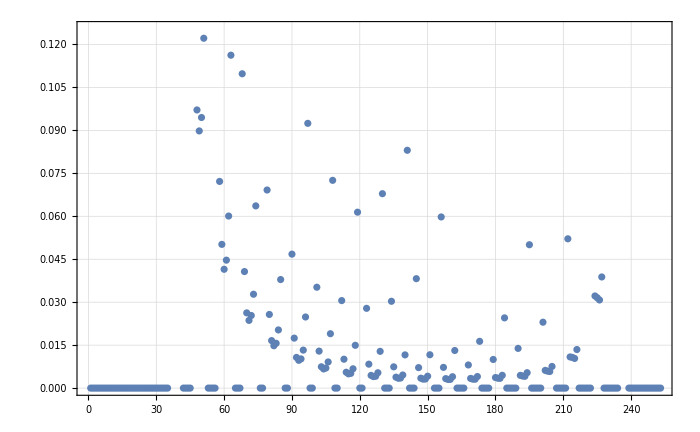

```mathematica
ListPlot[If[#==0,0,Sqrt[#]/#//N]&/@DetTableYHalf]
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],If[#==0,0,Sqrt[#]/#//N]&/@DetTableYHalf}],PlotRange->{0,0.01}]
```

-Graphics3D-

## Get Transfer Result

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport"]
```

/home/dmoser/eclipse-workspace/TransportProject/MergerTransport

```mathematica
(*ResultG=Import["/home/dmoser/eclipse-workspace/TransportProject/MergerTransport/TransferResult_18-08-20_b0_NC_DY_opt_G_1-192.txt","Table"];*)
```

```mathematica
(*ResultD=Import["/home/dmoser/eclipse-workspace/TransportProject/MergerTransport/TransferResult_18-08-20_b0_NC_DY_opt_193-253.txt","Table"];*)
```

```mathematica
(*Result=Join[ResultG,ResultD];*)
```

```mathematica
FileSorter[Directory_]:=Module[
{filenames=FileNames["TransferResult*",Directory],splitted,orderedlist},
splitted=StringSplit[filenames,"-"];
orderedlist=Ordering[ToExpression[StringTake[splitted[[All,-1]],{1,-5}]]];
filenames[[orderedlist]]
]
```

```mathematica
SubFileNames0=FileSorter["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_dMCRef/b0/"]
```

{~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_dMCRef/b0/TransferResult_08-09-20_NC_opt_D_BSOn_dMCRef_b0_1-98.txt,~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_dMCRef/b0/TransferResult_08-09-20_NC_opt_C_BSOn_dMCRef_b0_99-106.txt,~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_dMCRef/b0/TransferResult_08-09-20_NC_opt_C_BSOn_dMCRef_b0_107-122.txt,~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_dMCRef/b0/TransferResult_08-09-20_NC_opt_C_BSOn_dMCRef_b0_123-138.txt,~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_dMCRef/b0/TransferResult_08-09-20_NC_opt_C_BSOn_dMCRef_b0_139-154.txt,~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_dMCRef/b0/TransferResult_08-09-20_NC_opt_C_BSOn_dMCRef_b0_155-178.txt,~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_dMCRef/b0/TransferResult_08-09-20_NC_opt_D_BSOn_dMCRef_b0_179-253.txt}

```mathematica
Result=Flatten[Import[#,"Table"]&/@SubFileNames0,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],Result[[All,2]]/Total[Result[[All,2]]]}],PlotRange->All]
```

-Graphics3D-

## Compare

```mathematica
Show[
ListPlot3D[
Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]]-0.001,Result[[All,2]]/Total[Result[[All,2]]]}],
PlotRange->All,AxesLabel->{"x","y","#"},PlotStyle->Opacity[0.5]],

ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],DetTableYHalf/Total[DetTableYHalf]}],PlotRange->All,PlotStyle->Directive[Blue,Opacity[0.5]]]
]
```

-Graphics3D-

### manual chi2 with error estimate

```mathematica
Total[DetTableYHalf]
```

2627032

```mathematica
DetTableYHalfNormed=DetTableYHalf/Total[DetTableYHalf];
```

```mathematica
ResultNorm=Total[Result[[All,2]]]
```

2.34948

```mathematica
ResultNormed=Result[[All,2]]/Total[Result[[All,2]]];
```

```mathematica
Prec=3;Acc=4;
```

```mathematica
Sigma=Max[10^-Acc,#*10^-Prec]&/@Result[[All,2]];
```

```mathematica
SigmaNormed=Sigma/ResultNorm;
```

```mathematica
chi2=Total[(DetTableYHalfNormed-ResultNormed)^2/SigmaNormed^2]/252
```

168.405

```mathematica
InterpolMCData=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],DetTableYHalf/Total[DetTableYHalf]}],InterpolationOrder->1];
```

```mathematica
InterpolResult=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],Result[[All,2]]/Total[Result[[All,2]]]}],InterpolationOrder->1];
```

```mathematica
Plot3D[{InterpolMCData[x,y],InterpolResult[x,y]},{x,-0.04,0.04},{y,-0.04,0.04}]
```

-Graphics3D-

### load viridis

```mathematica
viridis=Module[{colorlist},colorlist={{0.26700401,0.00487433,0.32941519},{0.26851048,0.00960483,0.33542652},{0.26994384,0.01462494,0.34137895},{0.27130489,0.01994186,0.34726862},{0.27259384,0.02556309,0.35309303},{0.27380934,0.03149748,0.35885256},{0.27495242,0.03775181,0.36454323},{0.27602238,0.04416723,0.37016418},{0.2770184,0.05034437,0.37571452},{0.27794143,0.05632444,0.38119074},{0.27879067,0.06214536,0.38659204},{0.2795655,0.06783587,0.39191723},{0.28026658,0.07341724,0.39716349},{0.28089358,0.07890703,0.40232944},{0.28144581,0.0843197,0.40741404},{0.28192358,0.08966622,0.41241521},{0.28232739,0.09495545,0.41733086},{0.28265633,0.10019576,0.42216032},{0.28291049,0.10539345,0.42690202},{0.28309095,0.11055307,0.43155375},{0.28319704,0.11567966,0.43611482},{0.28322882,0.12077701,0.44058404},{0.28318684,0.12584799,0.44496},{0.283072,0.13089477,0.44924127},{0.28288389,0.13592005,0.45342734},{0.28262297,0.14092556,0.45751726},{0.28229037,0.14591233,0.46150995},{0.28188676,0.15088147,0.46540474},{0.28141228,0.15583425,0.46920128},{0.28086773,0.16077132,0.47289909},{0.28025468,0.16569272,0.47649762},{0.27957399,0.17059884,0.47999675},{0.27882618,0.1754902,0.48339654},{0.27801236,0.18036684,0.48669702},{0.27713437,0.18522836,0.48989831},{0.27619376,0.19007447,0.49300074},{0.27519116,0.1949054,0.49600488},{0.27412802,0.19972086,0.49891131},{0.27300596,0.20452049,0.50172076},{0.27182812,0.20930306,0.50443413},{0.27059473,0.21406899,0.50705243},{0.26930756,0.21881782,0.50957678},{0.26796846,0.22354911,0.5120084},{0.26657984,0.2282621,0.5143487},{0.2651445,0.23295593,0.5165993},{0.2636632,0.23763078,0.51876163},{0.26213801,0.24228619,0.52083736},{0.26057103,0.2469217,0.52282822},{0.25896451,0.25153685,0.52473609},{0.25732244,0.2561304,0.52656332},{0.25564519,0.26070284,0.52831152},{0.25393498,0.26525384,0.52998273},{0.25219404,0.26978306,0.53157905},{0.25042462,0.27429024,0.53310261},{0.24862899,0.27877509,0.53455561},{0.2468114,0.28323662,0.53594093},{0.24497208,0.28767547,0.53726018},{0.24311324,0.29209154,0.53851561},{0.24123708,0.29648471,0.53970946},{0.23934575,0.30085494,0.54084398},{0.23744138,0.30520222,0.5419214},{0.23552606,0.30952657,0.54294396},{0.23360277,0.31382773,0.54391424},{0.2316735,0.3181058,0.54483444},{0.22973926,0.32236127,0.54570633},{0.22780192,0.32659432,0.546532},{0.2258633,0.33080515,0.54731353},{0.22392515,0.334994,0.54805291},{0.22198915,0.33916114,0.54875211},{0.22005691,0.34330688,0.54941304},{0.21812995,0.34743154,0.55003755},{0.21620971,0.35153548,0.55062743},{0.21429757,0.35561907,0.5511844},{0.21239477,0.35968273,0.55171011},{0.2105031,0.36372671,0.55220646},{0.20862342,0.36775151,0.55267486},{0.20675628,0.37175775,0.55311653},{0.20490257,0.37574589,0.55353282},{0.20306309,0.37971644,0.55392505},{0.20123854,0.38366989,0.55429441},{0.1994295,0.38760678,0.55464205},{0.1976365,0.39152762,0.55496905},{0.19585993,0.39543297,0.55527637},{0.19410009,0.39932336,0.55556494},{0.19235719,0.40319934,0.55583559},{0.19063135,0.40706148,0.55608907},{0.18892259,0.41091033,0.55632606},{0.18723083,0.41474645,0.55654717},{0.18555593,0.4185704,0.55675292},{0.18389763,0.42238275,0.55694377},{0.18225561,0.42618405,0.5571201},{0.18062949,0.42997486,0.55728221},{0.17901879,0.43375572,0.55743035},{0.17742298,0.4375272,0.55756466},{0.17584148,0.44128981,0.55768526},{0.17427363,0.4450441,0.55779216},{0.17271876,0.4487906,0.55788532},{0.17117615,0.4525298,0.55796464},{0.16964573,0.45626209,0.55803034},{0.16812641,0.45998802,0.55808199},{0.1666171,0.46370813,0.55811913},{0.16511703,0.4674229,0.55814141},{0.16362543,0.47113278,0.55814842},{0.16214155,0.47483821,0.55813967},{0.16066467,0.47853961,0.55811466},{0.15919413,0.4822374,0.5580728},{0.15772933,0.48593197,0.55801347},{0.15626973,0.4896237,0.557936},{0.15481488,0.49331293,0.55783967},{0.15336445,0.49700003,0.55772371},{0.1519182,0.50068529,0.55758733},{0.15047605,0.50436904,0.55742968},{0.14903918,0.50805136,0.5572505},{0.14760731,0.51173263,0.55704861},{0.14618026,0.51541316,0.55682271},{0.14475863,0.51909319,0.55657181},{0.14334327,0.52277292,0.55629491},{0.14193527,0.52645254,0.55599097},{0.14053599,0.53013219,0.55565893},{0.13914708,0.53381201,0.55529773},{0.13777048,0.53749213,0.55490625},{0.1364085,0.54117264,0.55448339},{0.13506561,0.54485335,0.55402906},{0.13374299,0.54853458,0.55354108},{0.13244401,0.55221637,0.55301828},{0.13117249,0.55589872,0.55245948},{0.1299327,0.55958162,0.55186354},{0.12872938,0.56326503,0.55122927},{0.12756771,0.56694891,0.55055551},{0.12645338,0.57063316,0.5498411},{0.12539383,0.57431754,0.54908564},{0.12439474,0.57800205,0.5482874},{0.12346281,0.58168661,0.54744498},{0.12260562,0.58537105,0.54655722},{0.12183122,0.58905521,0.54562298},{0.12114807,0.59273889,0.54464114},{0.12056501,0.59642187,0.54361058},{0.12009154,0.60010387,0.54253043},{0.11973756,0.60378459,0.54139999},{0.11951163,0.60746388,0.54021751},{0.11942341,0.61114146,0.53898192},{0.11948255,0.61481702,0.53769219},{0.11969858,0.61849025,0.53634733},{0.12008079,0.62216081,0.53494633},{0.12063824,0.62582833,0.53348834},{0.12137972,0.62949242,0.53197275},{0.12231244,0.63315277,0.53039808},{0.12344358,0.63680899,0.52876343},{0.12477953,0.64046069,0.52706792},{0.12632581,0.64410744,0.52531069},{0.12808703,0.64774881,0.52349092},{0.13006688,0.65138436,0.52160791},{0.13226797,0.65501363,0.51966086},{0.13469183,0.65863619,0.5176488},{0.13733921,0.66225157,0.51557101},{0.14020991,0.66585927,0.5134268},{0.14330291,0.66945881,0.51121549},{0.1466164,0.67304968,0.50893644},{0.15014782,0.67663139,0.5065889},{0.15389405,0.68020343,0.50417217},{0.15785146,0.68376525,0.50168574},{0.16201598,0.68731632,0.49912906},{0.1663832,0.69085611,0.49650163},{0.1709484,0.69438405,0.49380294},{0.17570671,0.6978996,0.49103252},{0.18065314,0.70140222,0.48818938},{0.18578266,0.70489133,0.48527326},{0.19109018,0.70836635,0.48228395},{0.19657063,0.71182668,0.47922108},{0.20221902,0.71527175,0.47608431},{0.20803045,0.71870095,0.4728733},{0.21400015,0.72211371,0.46958774},{0.22012381,0.72550945,0.46622638},{0.2263969,0.72888753,0.46278934},{0.23281498,0.73224735,0.45927675},{0.2393739,0.73558828,0.45568838},{0.24606968,0.73890972,0.45202405},{0.25289851,0.74221104,0.44828355},{0.25985676,0.74549162,0.44446673},{0.26694127,0.74875084,0.44057284},{0.27414922,0.75198807,0.4366009},{0.28147681,0.75520266,0.43255207},{0.28892102,0.75839399,0.42842626},{0.29647899,0.76156142,0.42422341},{0.30414796,0.76470433,0.41994346},{0.31192534,0.76782207,0.41558638},{0.3198086,0.77091403,0.41115215},{0.3277958,0.77397953,0.40664011},{0.33588539,0.7770179,0.40204917},{0.34407411,0.78002855,0.39738103},{0.35235985,0.78301086,0.39263579},{0.36074053,0.78596419,0.38781353},{0.3692142,0.78888793,0.38291438},{0.37777892,0.79178146,0.3779385},{0.38643282,0.79464415,0.37288606},{0.39517408,0.79747541,0.36775726},{0.40400101,0.80027461,0.36255223},{0.4129135,0.80304099,0.35726893},{0.42190813,0.80577412,0.35191009},{0.43098317,0.80847343,0.34647607},{0.44013691,0.81113836,0.3409673},{0.44936763,0.81376835,0.33538426},{0.45867362,0.81636288,0.32972749},{0.46805314,0.81892143,0.32399761},{0.47750446,0.82144351,0.31819529},{0.4870258,0.82392862,0.31232133},{0.49661536,0.82637633,0.30637661},{0.5062713,0.82878621,0.30036211},{0.51599182,0.83115784,0.29427888},{0.52577622,0.83349064,0.2881265},{0.5356211,0.83578452,0.28190832},{0.5455244,0.83803918,0.27562602},{0.55548397,0.84025437,0.26928147},{0.5654976,0.8424299,0.26287683},{0.57556297,0.84456561,0.25641457},{0.58567772,0.84666139,0.24989748},{0.59583934,0.84871722,0.24332878},{0.60604528,0.8507331,0.23671214},{0.61629283,0.85270912,0.23005179},{0.62657923,0.85464543,0.22335258},{0.63690157,0.85654226,0.21662012},{0.64725685,0.85839991,0.20986086},{0.65764197,0.86021878,0.20308229},{0.66805369,0.86199932,0.19629307},{0.67848868,0.86374211,0.18950326},{0.68894351,0.86544779,0.18272455},{0.69941463,0.86711711,0.17597055},{0.70989842,0.86875092,0.16925712},{0.72039115,0.87035015,0.16260273},{0.73088902,0.87191584,0.15602894},{0.74138803,0.87344918,0.14956101},{0.75188414,0.87495143,0.14322828},{0.76237342,0.87642392,0.13706449},{0.77285183,0.87786808,0.13110864},{0.78331535,0.87928545,0.12540538},{0.79375994,0.88067763,0.12000532},{0.80418159,0.88204632,0.11496505},{0.81457634,0.88339329,0.11034678},{0.82494028,0.88472036,0.10621724},{0.83526959,0.88602943,0.1026459},{0.84556056,0.88732243,0.09970219},{0.8558096,0.88860134,0.09745186},{0.86601325,0.88986815,0.09595277},{0.87616824,0.89112487,0.09525046},{0.88627146,0.89237353,0.09537439},{0.89632002,0.89361614,0.09633538},{0.90631121,0.89485467,0.09812496},{0.91624212,0.89609127,0.1007168},{0.92610579,0.89732977,0.10407067},{0.93590444,0.8985704,0.10813094},{0.94563626,0.899815,0.11283773},{0.95529972,0.90106534,0.11812832},{0.96489353,0.90232311,0.12394051},{0.97441665,0.90358991,0.13021494},{0.98386829,0.90486726,0.13689671},{0.99324789,0.90615657,0.1439362}};
Evaluate[Blend[RGBColor@@@colorlist,#]&]];
```

### make contour plots

```mathematica
MCMinMax=Ceiling[MinMax[DetTableYHalfNormed],0.001]
```

{0.,0.042}

```mathematica
TransferMinMax=Ceiling[MinMax[ResultNormed],0.001]
```

{0.,0.043}

```mathematica
MCContourPlot=ContourPlot[InterpolMCData[x,y],{x,-0.03,0.03},{y,-0.025,0.04},PlotRange->TransferMinMax,PlotLegends->BarLegend[{viridis[#]&,TransferMinMax},13,LabelStyle->25],Contours->13,ImageSize->500,ColorFunction->(viridis[#]&),BaseStyle->25,FrameLabel->{{"y (m)",None},{"x (m)","Normed MC Det. Signal OverHat[#](x,y)"}},AspectRatio->Automatic,FrameTicks->{{Automatic,None},{{-0.03,-0.015,0,0.015,0.03},None}}]
```

-Graphics-

```mathematica
(*Export["~/Dropbox/PhD/PhDLatex/Figures/MCContour.png",MCContourPlot,ImageResolution->450];*)
```

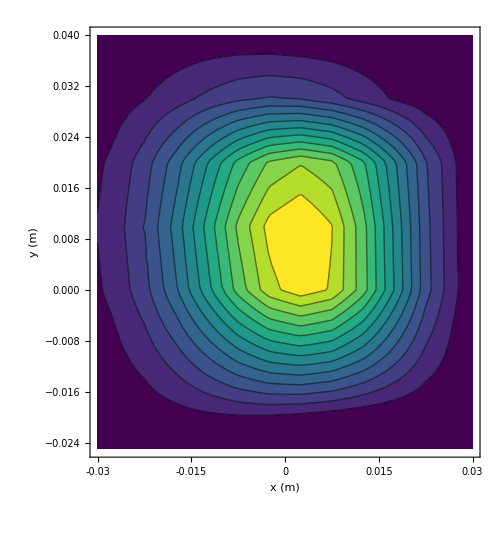

```mathematica
TransferContourPlot=ContourPlot[InterpolResult[x,y],{x,-0.03,0.03},{y,-0.025,0.04},PlotRange->TransferMinMax,(*PlotLegends->BarLegend[{viridis[#]&,TransferMinMax},13,LabelStyle->25],*)Contours->13,ImageSize->500,ColorFunction->(viridis[#]&),BaseStyle->25,FrameLabel->{{"y (m)",None},{"x (m)","Normed Transfer Ĝ(x,y)"}},AspectRatio->Automatic,FrameTicks->{{Automatic,None},{{-0.03,-0.015,0,0.015,0.03},None}}]
```

```mathematica
(*Export["~/Dropbox/PhD/PhDLatex/Figures/TransferContour.png",TransferContourPlot,ImageResolution->450];*)
```

### difference contour

```mathematica
DiffMinMax=Ceiling[MinMax[DetTableYHalfNormed-ResultNormed],0.0001]
```

{-0.0018,0.003}

```mathematica
53+36
```

89

```mathematica
DiffPlot=ContourPlot[InterpolMCData[x,y]-InterpolResult[x,y],{x,-0.03,0.03},{y,-0.025,0.04},PlotRange->DiffMinMax,Contours->19,BaseStyle->25,ImageSize->700,ColorFunction->(viridis[#]&),FrameLabel->{{"y (m)",None},{"x (m)",None}},AspectRatio->Automatic,FrameTicks->{{Automatic,None},{{-0.03,-0.015,0,0.015,0.03},None}},PlotLegends->BarLegend[{viridis[#]&,DiffMinMax},19,LabelStyle->25,LegendLabel->"OverHat[#](x,y)-Ĝ(x,y)"]]
```

-Graphics-

```mathematica
DiffMinMax={-0.0018,0.0028};
```

```mathematica
DiffPlot2=ListContourPlot[Flatten[Table[{x,y,InterpolMCData[x,y]-InterpolResult[x,y]},{x,-0.03,0.03,0.005},{y,-0.025,0.04,0.005}],1],PlotRange->DiffMinMax,Contours->19,InterpolationOrder->1,BaseStyle->25,ImageSize->700,ColorFunction->(viridis[#]&),FrameLabel->{{"y (m)",None},{"x (m)",None}},AspectRatio->Automatic,FrameTicks->{{Automatic,None},{{-0.03,-0.015,0,0.015,0.03},None}},PlotLegends->BarLegend[{viridis[#]&,DiffMinMax},19,LabelStyle->25,LegendLabel->"OverHat[#](x,y)-Ĝ(x,y)"]]
```

-Graphics-

```mathematica
(*Export["~/Dropbox/PhD/PhDLatex/Figures/MCTransferDiffContour.png",DiffPlot2,ImageResolution->450];*)
```

### shift the transfer result

```mathematica
{
Min[Table[InterpolMCData[x,y]-InterpolResult[x,y+0.002],{x,-0.03,0.03,0.005},{y,-0.025,0.035,0.01}]//Flatten],Max[Table[InterpolMCData[x,y]-InterpolResult[x,y+0.002],{x,-0.03,0.03,0.005},{y,-0.025,0.035,0.01}]//Flatten]
}
```

{-0.00162185,0.00279846}

```mathematica
extremafunc[yshift_?NumericQ]:={FindMinimum[{InterpolMCData[x,y]-InterpolResult[x,y+yshift],-0.03<x<0.03&&-0.025<y<0.035},{x,y},MaxIterations->4000][[1]],FindMaximum[{InterpolMCData[x,y]-InterpolResult[x,y+yshift],-0.03<x<0.03&&-0.025<y<0.035},{x,y},MaxIterations->4000][[1]]}
```

```mathematica
extremafunc[0.0006]
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 4000 iterations.

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 4000 iterations.

{-0.00133852,0.001775}

```mathematica
DiffMinMaxShifted=extremafunc[0.0012]
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 4000 iterations.

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 4000 iterations.

{-0.00196989,0.00280845}

```mathematica
extremafunc[0.00125]
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 4000 iterations.

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 4000 iterations.

{-0.00194189,0.00271147}

```mathematica
extrematotal[yshift_?NumericQ]:=Module[{val=extremafunc[yshift]},Total[Abs[val]]]
```

```mathematica
extrematotal[0.00055]
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 4000 iterations.

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 4000 iterations.

0.00309689

```mathematica
extrematotal[0.0006]
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 4000 iterations.

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 4000 iterations.

0.00311353

```mathematica
extrematotal[0.00065]
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 4000 iterations.

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 4000 iterations.

0.0031802

```mathematica
extrematotal[0.0007]
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 4000 iterations.

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 4000 iterations.

0.00324831

```mathematica
extrematotal[0.00]
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 4000 iterations.

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 4000 iterations.

0.00886456

```mathematica
extrematotal[0.002]
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 4000 iterations.

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 4000 iterations.

0.00299764

```mathematica
extremafunc2[yshift_?NumericQ]:=-Min[Table[InterpolMCData[x,y]-InterpolResult[x,y+yshift],{x,-0.03,0.03,0.005},{y,-0.025,0.035,0.01}]//Flatten]+Max[Table[InterpolMCData[x,y]-InterpolResult[x,y+yshift],{x,-0.03,0.03,0.005},{y,-0.025,0.035,0.01}]//Flatten]
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 4000 iterations.

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 4000 iterations.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 4000 iterations.

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 4000 iterations.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 4000 iterations.

General::stop: Further output of FindMinimum::cvmit will be suppressed during this calculation.

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 4000 iterations.

General::stop: Further output of FindMaximum::cvmit will be suppressed during this calculation.

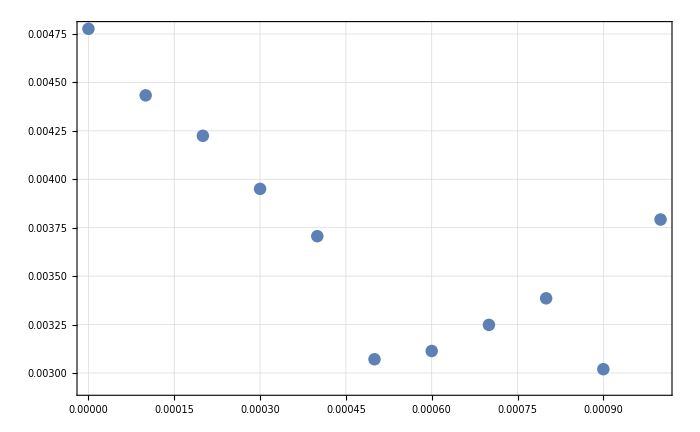

```mathematica
ListPlot[Table[{yshift,extrematotal[yshift]},{yshift,-0.00,0.001,0.0001}]]
```

```mathematica
DiffMinMaxShifted=Round[DiffMinMaxShifted,0.0001]
```

{-0.002,0.0028}

```mathematica
DiffMinMaxShifted={-0.0015,0.0019}
```

{-0.0015,0.0019}

```mathematica
ContourPlot[InterpolMCData[x,y]-InterpolResult[x,y+0.00065],{x,-0.03,0.03},{y,-0.025,0.04},PlotRange->DiffMinMaxShifted,Contours->16,BaseStyle->25,ImageSize->700,ColorFunction->(viridis[#]&),FrameLabel->{{"y (m)",None},{"x (m)",None}},AspectRatio->Automatic,FrameTicks->{{Automatic,None},{{-0.03,-0.015,0,0.015,0.03},None}},PlotLegends->BarLegend[{viridis[#]&,DiffMinMaxShifted},16,LabelStyle->25,LegendLabel->"OverHat[#](x,y)-Ĝ(x,y+0.6 mm)"]]
```

-Graphics-

### shift also in x

```mathematica
DiffMinMaxShifted2={-0.0013,0.0015}
```

{-0.0013,0.0015}

```mathematica
DiffContourXYShift=ContourPlot[InterpolMCData[x,y]-InterpolResult[x-0.0005,y+0.00065],{x,-0.03,0.03},{y,-0.025,0.04},PlotRange->DiffMinMaxShifted2,Contours->15,BaseStyle->25,ImageSize->700,ColorFunction->(viridis[#]&),FrameLabel->{{"y (m)",None},{"x (m)",None}},AspectRatio->Automatic,FrameTicks->{{Automatic,None},{{-0.03,-0.015,0,0.015,0.03},None}},PlotLegends->BarLegend[{viridis[#]&,DiffMinMaxShifted2},15,LabelStyle->25,LegendLabel->"OverHat[#](x,y)-Ĝ(x-0.5 mm,y+0.65 mm)"]]
```

-Graphics-

```mathematica
Export["~/Dropbox/PhD/PhDLatex/Figures/MCTransferDiffContour_XYShift.png",DiffContourXYShift,ImageResolution->450];
```

### first tabling, then list plotting

```mathematica
DiffMinMaxShifted2={-0.0012,0.0013}
```

{-0.0012,0.0013}

```mathematica
DiffContourXYShift=ListContourPlot[Flatten[Table[{x,y,InterpolMCData[x,y]-InterpolResult[x-0.0005,y+0.00065]},{x,-0.03,0.03,0.005},{y,-0.025,0.035,0.005}],1],InterpolationOrder->1,PlotRange->DiffMinMaxShifted2,Contours->15,BaseStyle->25,ImageSize->700,ColorFunction->(viridis[#]&),FrameLabel->{{"y (m)",None},{"x (m)",None}},AspectRatio->Automatic,FrameTicks->{{Automatic,None},{{-0.03,-0.015,0,0.015,0.03},None}},PlotLegends->BarLegend[{viridis[#]&,DiffMinMaxShifted2},15,LabelStyle->25,LegendLabel->"OverHat[#](x,y)-Ĝ(x+x_C,y+y_C)"]]
```

-Graphics-

### mean deviation

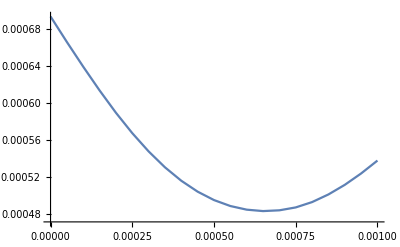

```mathematica
ListLinePlot[Table[{yshift,Mean[Table[Abs[InterpolMCData[x,y]-InterpolResult[x,y+yshift]],{x,-0.03,0.03,0.00001},{y,-0.025,0.04,0.00001}]//Flatten]},{yshift,0.00,0.001,0.00005}]]
```

```mathematica
FindMaximum[{Abs[(InterpolMCData[x,y]-InterpolResult[x,y])],-0.04<x<0.04&&-0.04<y<0.04},{x,y}]
```

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{0.00362703,{x→-0.00242304,y→0.029999}}

```mathematica
ClearAll[maxfunc]
```

```mathematica
maxfunc[yshift_?NumericQ]:=FindMaximum[{Abs[(InterpolMCData[x,y]-InterpolResult[x,y+yshift])],-0.04<x<0.04&&-0.04<y<0.04},{x,y}][[1]]
```

```mathematica
FindMinimum[{maxfunc[yShift],-0.0015<yShift<0.0015},yShift]
```

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

General::stop: Further output of FindMaximum::cvmit will be suppressed during this calculation.

$Aborted

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

General::stop: Further output of FindMaximum::cvmit will be suppressed during this calculation.

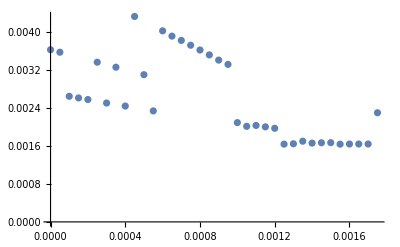

```mathematica
ListPlot[Table[{yshift,maxfunc[yshift]},{yshift,-0.000,0.00175,0.00005}]]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

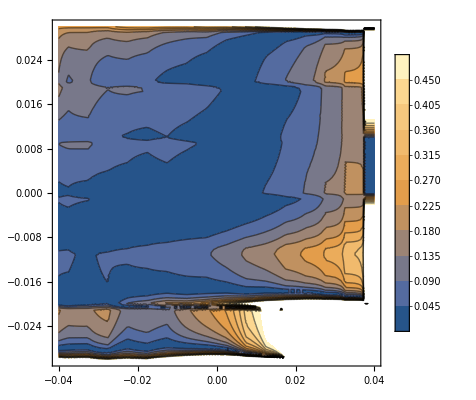

```mathematica
ContourPlot[Abs[(InterpolMCData[x,y]-InterpolResult[x,y+0.001])/InterpolMCData[x,y]],{x,-0.04,0.04},{y,-0.03,0.03},PlotRange->{0,0.5},PlotLegends->Automatic,Contours->10]
```

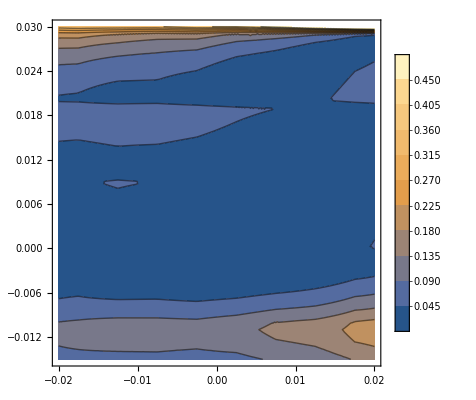

```mathematica
ContourPlot[Abs[(InterpolMCData[x,y]-InterpolResult[x,y+0.001])/InterpolMCData[x,y]],{x,-0.02,0.02},{y,-0.015,0.03},PlotRange->{0,0.5},PlotLegends->Automatic,Contours->10]
```

### y plots for correct shift

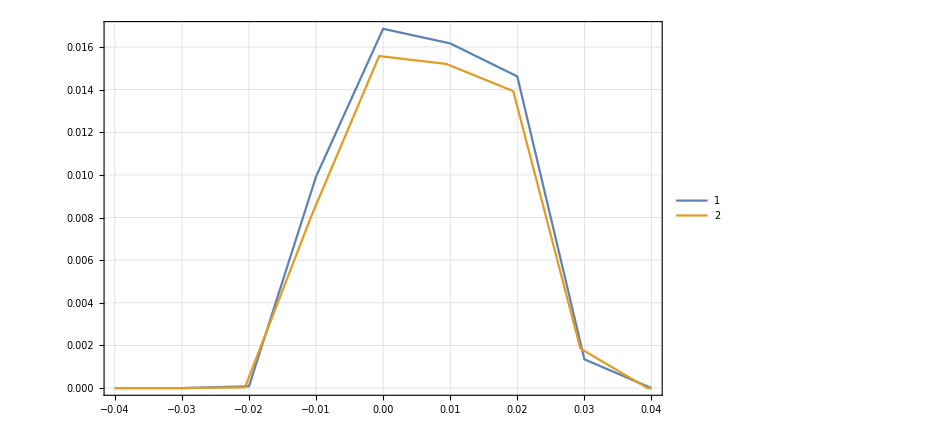

```mathematica
Plot[{InterpolMCData[0.02,y],InterpolResult[0.02,y+0.0006]},{y,-0.04,0.04},PlotRange->All,PlotLegends->Automatic]
```

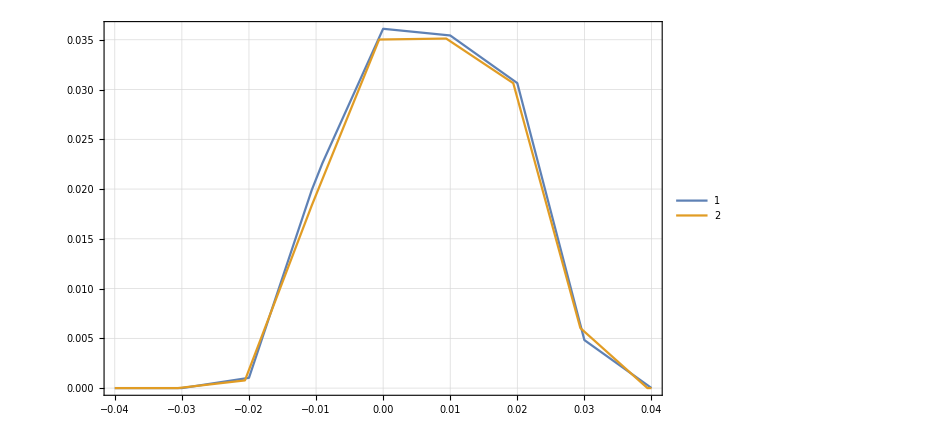

```mathematica
Plot[{InterpolMCData[0.01,y],InterpolResult[0.01,y+0.0006]},{y,-0.04,0.04},PlotRange->All,PlotLegends->Automatic]
```

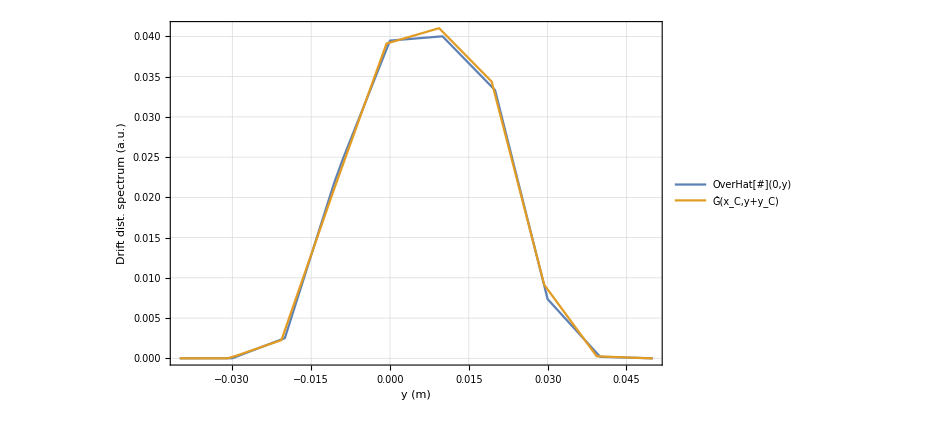

```mathematica
YDriftComparePlotShifted=Plot[{InterpolMCData[0.,y],InterpolResult[0.-0.0005,y+0.00065]},{y,-0.04,0.05},PlotRange->All,PlotLegends->Placed[LineLegend[{"OverHat[#](0,y)","Ĝ(x_C,y+y_C)"},LabelStyle->25,LegendFunction->(Framed[#1, FrameMargins -> 0,Background->White] & )],{0.2,0.8}],BaseStyle->25,FrameLabel->{{"Drift dist. spectrum (a.u.)",None},{"y (m)",None}}]
```

```mathematica
Export["~/Dropbox/PhD/PhDLatex/Figures/YDriftComparePlotShifted.png",YDriftComparePlotShifted,ImageResolution->450];
```

### in x

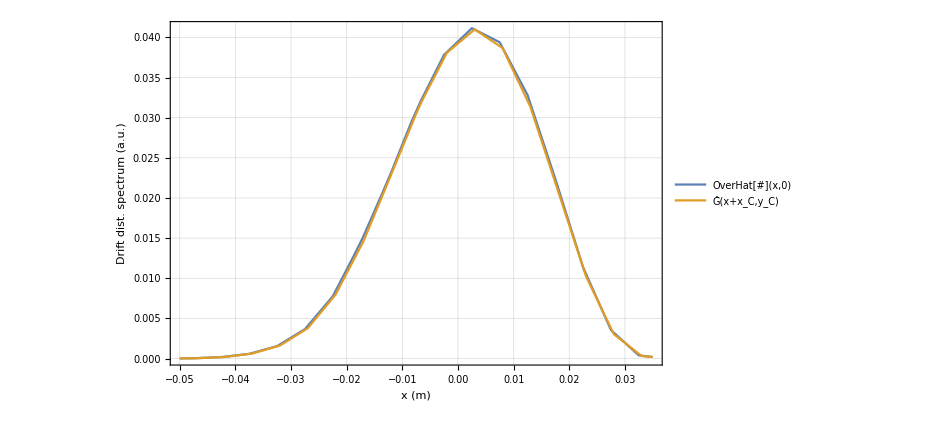

```mathematica
XDriftComparePlotShifted=Plot[{InterpolMCData[x,0.],InterpolResult[x-0.0005,0.00065]},{x,-0.05,0.035},PlotRange->All,PlotLegends->Placed[LineLegend[{"OverHat[#](x,0)","Ĝ(x+x_C,y_C)"},LabelStyle->25,LegendFunction->(Framed[#1, FrameMargins -> 0,Background->White] & )],{0.2,0.8}],BaseStyle->25,FrameLabel->{{"Drift dist. spectrum (a.u.)",None},{"x (m)",None}}]
```

```mathematica
Export["~/Dropbox/PhD/PhDLatex/Figures/XDriftComparePlotShifted.png",XDriftComparePlotShifted,ImageResolution->450];
```

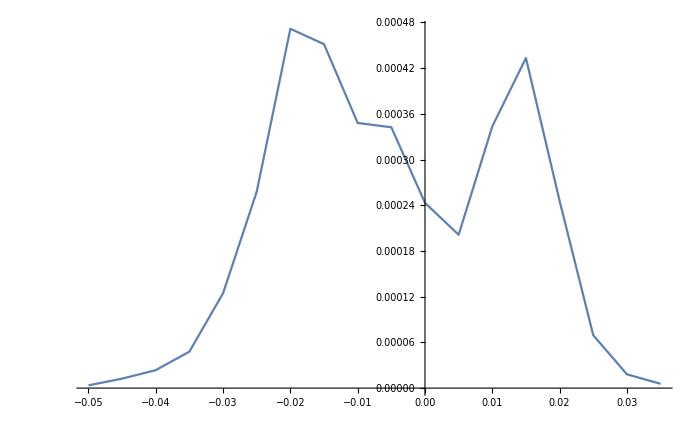

```mathematica
ListLinePlot[Table[{x,InterpolMCData[x,0.]-InterpolResult[x-0.0005,0.00065]},{x,-0.05,0.035,0.005}],PlotRange->All,PlotLegends->Automatic]
```

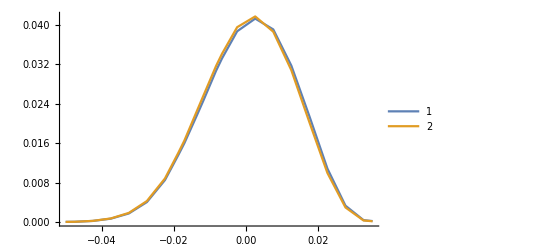

```mathematica
Plot[{InterpolMCData[x,0.01],InterpolResult[x,0.01+0.0012]},{x,-0.05,0.035},PlotRange->All,PlotLegends->Automatic]
```

# Transfer Sensitivity Investigations (evaluate this first)

## 0 spectrum

### algorithm to sort files according to last binnumber

```mathematica
FileSorter[Directory_]:=Module[
{filenames=FileNames["TransferResult*",Directory],splitted,orderedlist},
splitted=StringSplit[filenames,"-"];
orderedlist=Ordering[ToExpression[StringTake[splitted[[All,-1]],{1,-5}]]];
filenames[[orderedlist]]
]
```

```mathematica
SubFileNames0=FileSorter["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_d0/b0/"]
```

{~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_d0/b0/TransferResult_08-09-20_NC_opt_D_BSOn_d0_b0_1-96.txt,~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_d0/b0/TransferResult_08-09-20_NC_opt_D_BSOn_d0_b0_97-112.txt,~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_d0/b0/TransferResult_08-09-20_NC_opt_D_BSOn_d0_b0_113-128.txt,~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_d0/b0/TransferResult_08-09-20_NC_opt_D_BSOn_d0_b0_129-144.txt,~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_d0/b0/TransferResult_08-09-20_NC_opt_D_BSOn_d0_b0_145-160.txt,~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_d0/b0/TransferResult_08-09-20_NC_opt_D_BSOn_d0_b0_161-176.txt,~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_d0/b0/TransferResult_08-09-20_NC_opt_D_BSOn_d0_b0_177-192.txt,~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_d0/b0/TransferResult_08-09-20_NC_opt_D_BSOn_d0_b0_193-253.txt}

```mathematica
RefSpectrum=Flatten[Table[Import[SubFileNames0[[i]],"Table"],{i,1,8}],1];
```

### show single core timing

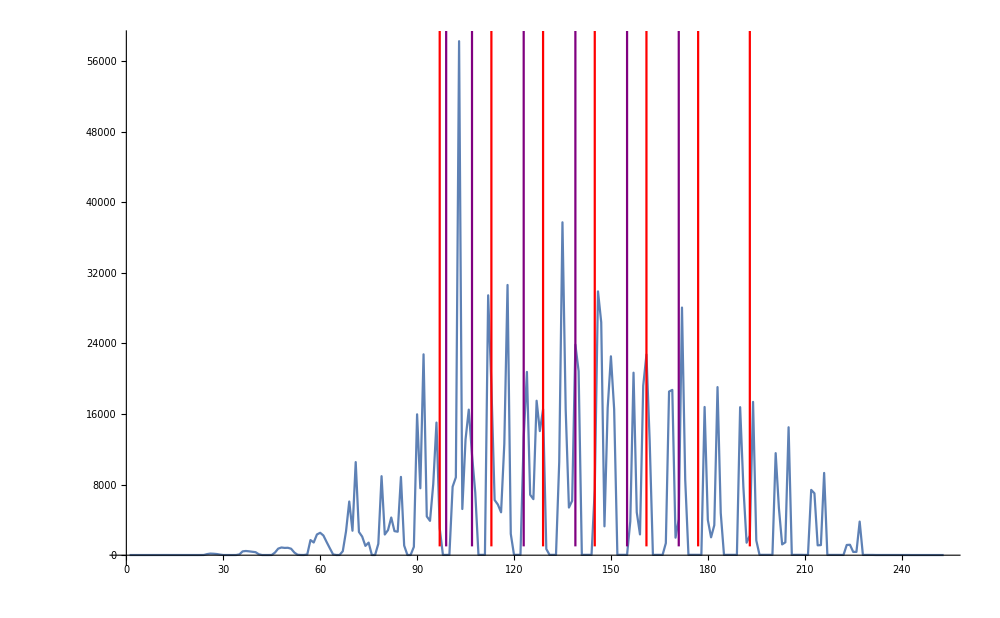

```mathematica
Show[
ListLinePlot[RefSpectrum[[All,1]],PlotRange->All,ImageSize->1000],
ParametricPlot[{{97,1000*d},{113,1000*d},{129,1000*d},{145,1000*d},{161,1000*d},{177,1000*d},{193,1000*d}},{d,1,253},PlotStyle->Red],
ParametricPlot[{{99,1000*d},{107,1000*d},{123,1000*d},{139,1000*d},{155,1000*d},{171,1000*d}},{d,1,253},PlotStyle->Purple]
]
```

## get Bin data

```mathematica
MCFolder="~/ClusterMC_v4/NoMoS_Danfysik_25-02-19_reduceTypes_smallerDV4/";
```

```mathematica
DetHisto=Import[MCFolder<>"GlobalTransferData/"<>"DetXYHistSum.txt","Table"]
```

{{-0.07,-0.065,-0.06,-0.055,-0.05,-0.045,-0.04,-0.035,-0.03,-0.025,-0.02,-0.015,-0.01,-0.005,1.38778×10^-17,0.005,0.01,0.015,0.02,0.025,0.03,0.035,0.04,0.045},{-1.054,-1.049,-1.044,-1.039,-1.034,-1.029,-1.024,-1.019,-1.014,-1.009,-1.004,-0.999002,-0.994002,-0.989002,-0.984002,-0.979002,-0.974002,-0.969002,-0.964002,-0.959002,-0.954002,-0.949002,-0.944002},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,4,5,5,8,10,8,8,6,7,1,2,0,0,0,0,0,0,0},{0,0,0,2,10,21,53,53,54,70,54,58,46,21,8,3,0,0,0,0,0,0},{0,0,0,25,53,139,172,225,286,295,273,228,180,97,55,19,2,0,0,0,0,0},{0,0,17,66,190,414,617,832,888,901,832,724,556,375,198,49,14,1,0,0,0,0},{0,1,34,175,526,986,1611,2023,2292,2277,2214,1873,1477,947,504,192,41,1,0,0,0,0},{0,3,88,369,1087,2197,3813,4904,5250,5381,5155,4475,3545,2138,1186,436,106,11,0,0,0,0},{0,1,110,696,1886,4112,7968,10086,11143,11228,10855,9519,7598,4390,2004,769,181,9,0,0,0,0},{0,1,155,916,2905,6920,14467,18151,19991,20436,19831,18072,14297,7701,3307,1174,253,12,0,0,0,0},{0,2,119,1170,3997,10330,22455,28438,30617,31268,30614,28053,23025,11808,4634,1437,214,3,0,0,0,0},{0,0,61,1027,4717,13435,30336,38438,41907,42599,41926,39417,31810,16031,5781,1657,145,0,0,0,0,0},{0,0,11,674,4489,15048,36916,46817,50520,51226,51068,48296,39189,18713,6111,1268,47,0,0,0,0,0},{0,0,0,280,3692,15404,40139,51198,53790,54718,55258,52828,43694,19608,5208,594,0,0,0,0,0,0},{0,0,0,34,2219,13116,38833,48711,51342,51399,52013,51454,43194,18067,3567,184,0,0,0,0,0,0},{0,0,0,1,804,9211,32451,41018,41357,42074,43057,43175,36185,13879,1648,15,0,0,0,0,0,0},{0,0,0,0,155,5049,22938,27689,28143,28324,29185,29578,26021,8580,399,0,0,0,0,0,0,0},{0,0,0,0,7,1882,12109,14079,14010,14468,14745,15047,13718,3798,44,0,0,0,0,0,0,0},{0,0,0,0,0,368,3929,4520,4297,4409,4603,4715,4490,1028,0,0,0,0,0,0,0,0},{0,0,0,0,0,18,475,491,468,537,499,557,553,111,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,4,0,0,1,0,1,4,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
InfoFile=Import[MCFolder<>"info.txt","Table"];
```

```mathematica
R=InfoFile[[1,2]]
```

0.999002

### Get XY Bins with Ybins halfed

```mathematica
XYBinBoundariesYHalf=Flatten[Table[
{
{DetHisto[[1,xi]],DetHisto[[1,xi+1]]},
{-DetHisto[[2,yi+2]]-R,-DetHisto[[2,yi]]-R}
},{xi,1,Length[DetHisto[[1]]]-1,1},{yi,1,Length[DetHisto[[2]]]-2,2}],1];
```

```mathematica
Length[XYBinBoundariesYHalf]
```

253

```mathematica
Get["NeutronBeam/XYBinIntBoundaries.m"]
```

```mathematica
XYBinCentersYHalf=BinCenters[XYBinBoundariesYHalf];
```

## check spectrum

```mathematica
Transfer3DPlot=ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}],PlotRange->{{-0.04,0.04},{-0.04,0.04},All},BaseStyle->20,ImageSize->600,AxesLabel->{"x (m)","y (m)","Ĝ(x_bin,y_bin)"},InterpolationOrder->1]
```

-Graphics3D-

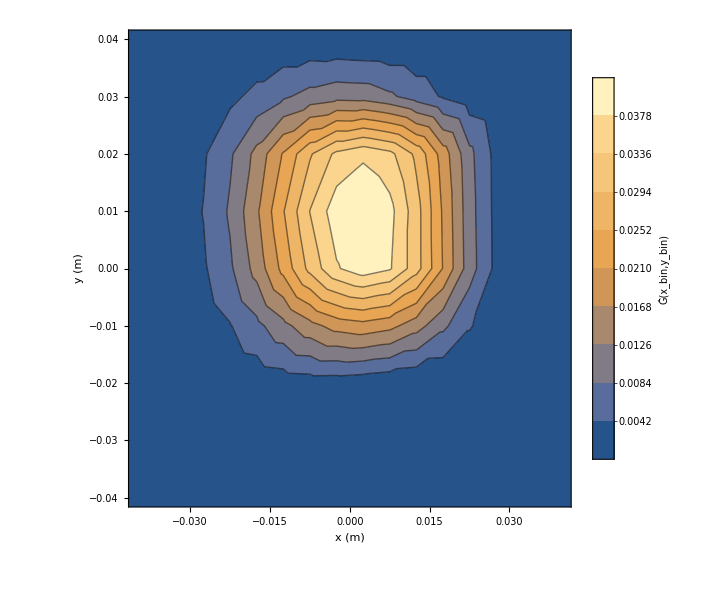

```mathematica
TransferContourPlot=ListContourPlot[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}],PlotRange->{{-0.04,0.04},{-0.04,0.04},All},BaseStyle->25,ImageSize->600,InterpolationOrder->1,Contours->9,FrameLabel->{{"y (m)",None},{"x (m)",None}},PlotLegends->BarLegend[Automatic,LabelStyle->25,LegendLabel->"Ĝ(x_bin,y_bin)"]]
```

```mathematica
(*Export["~/Dropbox/PhD/PhDLatex/Figures/Transfer3D.png",Transfer3DPlot,ImageResolution->450];
Export["~/Dropbox/PhD/PhDLatex/Figures/TransferContour.png",TransferContourPlot,ImageResolution->450];*)
```

# dBRxB, k=-15.13

### b=0

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_dB/b0/"];
```

```mathematica
dBRxBSubFileNamesb0=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_G_BSOn_dB_b0_1-96.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dB_b0_97-112.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dB_b0_113-128.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dB_b0_129-144.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dB_b0_145-160.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dB_b0_161-176.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dB_b0_177-192.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dB_b0_193-253.txt}

```mathematica
dBRxBSpectrumb0=Flatten[Table[Import[dBRxBSubFileNamesb0[[i]],"Table"],{i,1,8}],1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb0[[All,2]]}],PlotRange->All]*)
```

### b=15

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_dB/b15/"];
```

```mathematica
dBRxBSubFileNamesb15=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_C_BSOn_dB_b15_1-96.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dB_b15_97-112.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dB_b15_113-128.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dB_b15_129-144.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dB_b15_145-160.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dB_b15_161-176.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dB_b15_177-192.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dB_b15_193-253.txt}

```mathematica
dBRxBSpectrumb15=Flatten[Table[Import[dBRxBSubFileNamesb15[[i]],"Table"],{i,1,8}],1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb0[[All,2]]}],PlotRange->All]*)
```

### b=7.5

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_dB/b7/"];
```

```mathematica
dBRxBSubFileNamesb75=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_G_BSOn_dB_b7_1-96.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dB_b7_97-112.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dB_b7_113-128.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dB_b7_129-144.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dB_b7_145-160.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dB_b7_161-176.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dB_b7_177-192.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dB_b7_193-253.txt}

```mathematica
dBRxBSpectrumb75=Flatten[Table[Import[dBRxBSubFileNamesb75[[i]],"Table"],{i,1,8}],1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]}],PlotRange->All]*)
```

### b=-7.5

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_dB/b-7/"];
```

```mathematica
dBRxBSubFileNamesbm75=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_D_BSOn_dB_b-7_1-96.txt,TransferResult_08-09-20_NC_opt_D_BSOn_dB_b-7_97-112.txt,TransferResult_08-09-20_NC_opt_D_BSOn_dB_b-7_113-128.txt,TransferResult_08-09-20_NC_opt_D_BSOn_dB_b-7_129-144.txt,TransferResult_08-09-20_NC_opt_D_BSOn_dB_b-7_145-160.txt,TransferResult_08-09-20_NC_opt_D_BSOn_dB_b-7_161-176.txt,TransferResult_08-09-20_NC_opt_D_BSOn_dB_b-7_177-192.txt,TransferResult_08-09-20_NC_opt_D_BSOn_dB_b-7_193-253.txt}

```mathematica
dBRxBSpectrumbm75=Flatten[Table[Import[dBRxBSubFileNamesbm75[[i]],"Table"],{i,1,8}],1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumbm75[[All,2]]}],PlotRange->All]*)
```

### b=-15

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_dB/b-15/"];
```

```mathematica
dBRxBSubFileNamesbm15=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_C_BSOn_dB_b-15_1-96.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dB_b-15_97-112.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dB_b-15_113-128.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dB_b-15_129-144.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dB_b-15_145-160.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dB_b-15_161-176.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dB_b-15_177-192.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dB_b-15_193-253.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
dBRxBSpectrumbm15=Flatten[Import[#,"Table"]&/@dBRxBSubFileNamesbm15,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumbm15[[All,2]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumbm15[[All,2]]/Total[dBRxBSpectrumbm15[[All,2]]]}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],Boole[#≠0]&/@(RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]-dBRxBSpectrumb0[[All,2]]/Total[dBRxBSpectrumb0[[All,2]]])}],PlotRange->All]
```

-Graphics3D-

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}]];
```

```mathematica
Plot3D[RefSpectrumInter[x,y],{x,-0.05,0.04},{y,-0.05,0.05},PlotRange->All]
```

-Graphics3D-

```mathematica
dBRxBSpectrumb0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb0[[All,2]]/Total[dBRxBSpectrumb0[[All,2]]]}]];
```

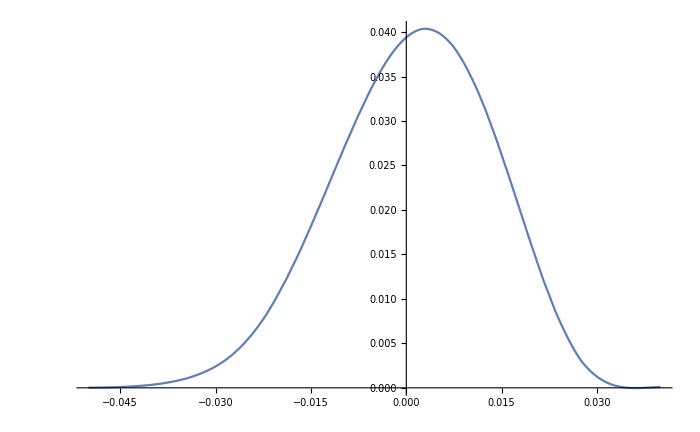

```mathematica
Plot[RefSpectrumInter[x,0.],{x,-0.05,0.04},PlotRange->All]
```

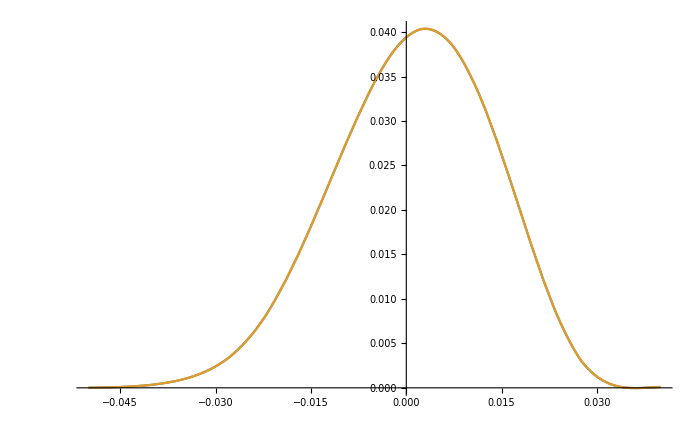

```mathematica
Plot[{RefSpectrumInter[x,0.],dBRxBSpectrumb0Inter[x,0.]},{x,-0.05,0.04},PlotRange->All]
```

```mathematica
dBRxBSpectrumb75Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb75[[All,2]]/Total[dBRxBSpectrumb75[[All,2]]]}]];
dBRxBSpectrumbm75Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumbm75[[All,2]]/Total[dBRxBSpectrumbm75[[All,2]]]}]];
dBRxBSpectrumb15Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb15[[All,2]]/Total[dBRxBSpectrumb15[[All,2]]]}]];
dBRxBSpectrumbm15Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumbm15[[All,2]]/Total[dBRxBSpectrumbm15[[All,2]]]}]];
```

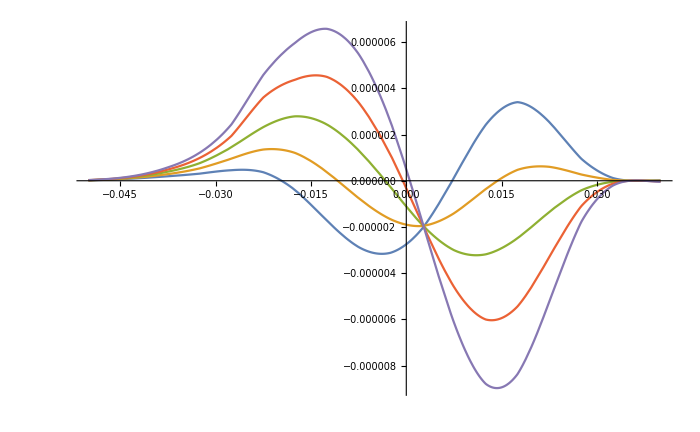

```mathematica
Plot[{
RefSpectrumInter[x,0.]-dBRxBSpectrumbm15Inter[x,0.],
RefSpectrumInter[x,0.]-dBRxBSpectrumbm75Inter[x,0.],
RefSpectrumInter[x,0.]-dBRxBSpectrumb0Inter[x,0.],
RefSpectrumInter[x,0.]-dBRxBSpectrumb75Inter[x,0.],
RefSpectrumInter[x,0.]-dBRxBSpectrumb15Inter[x,0.]
}
,{x,-0.05,0.04},PlotRange->All]
```

```mathematica
ListPlot[Total[(RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]-#)^2]&/@BRxBDataList]
```

ListPlot::lpn: BRxBDataList is not a list of numbers or pairs of numbers.

ListPlot[BRxBDataList]

```mathematica
dBRxBSpectrumb75[[All,2]]/Total[dBRxBSpectrumb75[[All,2]]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.36863×10^-10,4.07996×10^-10,3.19292×10^-11,1.42553×10^-13,0.,0.,0.,0.,0.,0.,2.59993×10^-9,1.4643×10^-7,3.11107×10^-7,2.31112×10^-7,1.36065×10^-7,4.76193×10^-8,1.2291×10^-9,0.,0.,0.,0.,2.03998×10^-7,3.11947×10^-6,6.84058×10^-6,6.62686×10^-6,4.83431×10^-6,1.93743×10^-6,1.46401×10^-7,0.,0.,0.,7.05888×10^-10,3.16048×10^-6,0.0000234196,0.0000493116,0.0000531614,0.0000408369,0.0000188314,2.86494×10^-6,9.03721×10^-9,0.,0.,3.23234×10^-7,0.0000177044,0.000100397,0.000205907,0.000234623,0.000186966,0.0000927304,0.0000185237,5.51569×10^-7,0.,0.,9.71469×10^-7,0.0000595062,0.000309378,0.000628561,0.000736105,0.000600097,0.000310256,0.0000712827,3.0292×10^-6,0.,0.,2.74528×10^-6,0.000152579,0.000774239,0.00159952,0.0018878,0.00156135,0.000823198,0.000199853,9.54737×10^-6,0.,0.,3.88467×10^-6,0.000313669,0.00168782,0.00369996,0.00433486,0.00363987,0.00190851,0.000449662,0.0000222802,0.,0.,0.,0.000531094,0.00323004,0.00773746,0.00898466,0.00770991,0.00398244,0.000844609,0.0000358352,0.,0.,0.,0.000740222,0.00535976,0.0139127,0.0161335,0.0141924,0.0072312,0.00135022,0.0000226273,0.,0.,0.,0.000863278,0.00775098,0.0214202,0.0249538,0.0223604,0.0112936,0.00185325,7.06033×10^-7,0.,0.,0.,0.000809817,0.00986941,0.0288684,0.0337018,0.0306964,0.0153352,0.00211014,0.,0.,0.,0.,0.00054451,0.0110646,0.0345881,0.0402363,0.0373612,0.0183953,0.00197547,0.,0.,0.,0.,0.000206637,0.0108394,0.0369185,0.0424076,0.0403525,0.0194847,0.00143803,0.,0.,0.,0.,0.0000203655,0.00914436,0.0348098,0.0391745,0.0382876,0.0180841,0.000732696,0.,0.,0.,0.,0.,0.00645827,0.0283774,0.0311792,0.0311918,0.014377,0.000241551,0.,0.,0.,0.,0.,0.00375251,0.019043,0.0204596,0.0208311,0.00937791,0.000013516,0.,0.,0.,0.,0.,0.00163446,0.00951662,0.0100221,0.0102987,0.00457549,0.,0.,0.,0.,0.,0.,0.000440399,0.00285973,0.00296835,0.00305719,0.00136139,0.,0.,0.,0.,0.,0.,0.0000450576,0.000308296,0.000317597,0.000327138,0.000146399,0.,0.,0.,0.,0.,0.,4.85721×10^-8,3.66074×10^-7,3.75038×10^-7,3.84282×10^-7,6.12352×10^-8,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFit]
```

```mathematica
Get["Common/CommonFunctions.m"]
```

```mathematica
BRxBDataList={dBRxBSpectrumbm15[[All,2]]/Total[dBRxBSpectrumbm15[[All,2]]],dBRxBSpectrumbm75[[All,2]]/Total[dBRxBSpectrumbm75[[All,2]]],dBRxBSpectrumb0[[All,2]]/Total[dBRxBSpectrumb0[[All,2]]],dBRxBSpectrumb75[[All,2]]/Total[dBRxBSpectrumb75[[All,2]]],dBRxBSpectrumb15[[All,2]]/Total[dBRxBSpectrumb15[[All,2]]]};
```

```mathematica
bList={-15,-7.5,0.,7.5,15}*10^-4.
```

{-0.0015,-0.00075,0.,0.00075,0.0015}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

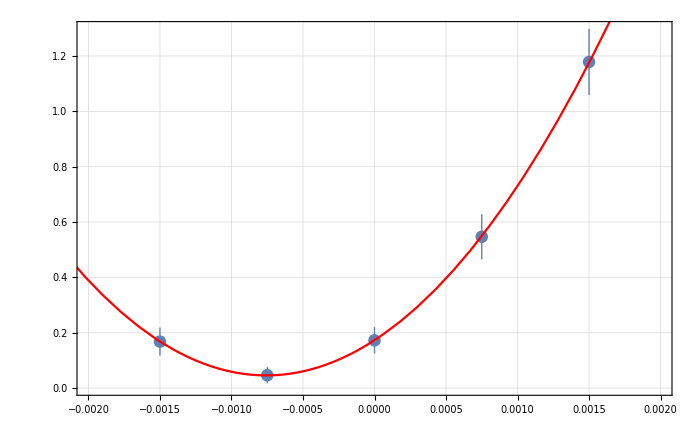
{{{1.67947×10^-10,4.64371×10^-11,1.7259×10^-10,5.46827×10^-10,1.17847×10^-9},{5.02571×10^-11,2.93313×10^-11,4.7551×10^-11,8.1608×10^-11,1.19841×10^-10}},b0 =  | -0.000756452
FittedModel[4.59438×10^-11+0.000221834 (0.000756452+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.000756452 | 0.0000982889 | -7.6962 | 0.016467
scale | 0.000221834 | 0.0000303947 | 7.29843 | 0.0182607
yoffset | 4.59438×10^-11 | 2.41516×10^-11 | 1.90231 | 0.197472 | 
 | DF | SS | MS
Model | 3 | 168.444 | 56.1481
Error | 2 | 0.00208928 | 0.00104464
Uncorrected Total | 5 | 168.447 | 
Corrected Total | 4 | 109.764 |  | ,-Graphics-}

```mathematica
BRxBInvest=TransferToRefParableFit[RefSpectrum[[All,2]],BRxBDataList,bList, 4]
```

```mathematica
BRxBInvest[[2,1,1,2]]/(5*10^-5)
```

-15.129

# dAlpha, k=18.84

```mathematica
dParameter="Alpha";
```

### b=0

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_d"<>dParameter<>"/b0/"];
```

```mathematica
dAlphaSubFileNamesb0=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_D_BSOn_dAlpha_b0_1-98.txt,TransferResult_08-09-20_NC_opt_D_BSOn_dAlpha_b0_99-106.txt,TransferResult_08-09-20_NC_opt_D_BSOn_dAlpha_b0_107-122.txt,TransferResult_08-09-20_NC_opt_D_BSOn_dAlpha_b0_123-138.txt,TransferResult_08-09-20_NC_opt_D_BSOn_dAlpha_b0_139-154.txt,TransferResult_08-09-20_NC_opt_D_BSOn_dAlpha_b0_155-170.txt,TransferResult_08-09-20_NC_opt_D_BSOn_dAlpha_b0_171-253.txt}

```mathematica
dAlphaSpectrumb0=Flatten[Import[#,"Table"]&/@dAlphaSubFileNamesb0,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb0[[All,2]]}],PlotRange->All]*)
```

### b=15

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_d"<>dParameter<>"/b15/"];
```

```mathematica
dAlphaSubFileNamesb15=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_G_BSOn_dAlpha_b15_1-98.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dAlpha_b15_99-106.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dAlpha_b15_107-122.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dAlpha_b15_123-138.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dAlpha_b15_139-154.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dAlpha_b15_155-170.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dAlpha_b15_171-253.txt}

```mathematica
dAlphaSpectrumb15=Flatten[Import[#,"Table"]&/@dAlphaSubFileNamesb15,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumb0[[All,2]]}],PlotRange->All]*)
```

### b=7.5

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_d"<>dParameter<>"/b7/"];
```

```mathematica
dAlphaSubFileNamesb75=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_C_BSOn_dAlpha_b7_1-98.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dAlpha_b7_99-106.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dAlpha_b7_107-122.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dAlpha_b7_123-138.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dAlpha_b7_139-154.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dAlpha_b7_155-170.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dAlpha_b7_171-253.txt}

```mathematica
dAlphaSpectrumb75=Flatten[Import[#,"Table"]&/@dAlphaSubFileNamesb75,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumb75[[All,2]]}],PlotRange->All]*)
```

### b=-7.5

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_d"<>dParameter<>"/b-7/"];
```

```mathematica
dAlphaSubFileNamesbm75=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_C_BSOn_dAlpha_b-7_1-98.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dAlpha_b-7_99-106.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dAlpha_b-7_107-122.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dAlpha_b-7_123-138.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dAlpha_b-7_139-154.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dAlpha_b-7_155-170.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dAlpha_b-7_171-253.txt}

```mathematica
dAlphaSpectrumbm75=Flatten[Import[#,"Table"]&/@dAlphaSubFileNamesbm75,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumbm75[[All,2]]}],PlotRange->All]*)
```

### b=-15

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_d"<>dParameter<>"/b-15/"];
```

```mathematica
dAlphaSubFileNamesbm15=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_G_BSOn_dAlpha_b-15_1-98.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dAlpha_b-15_99-106.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dAlpha_b-15_107-122.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dAlpha_b-15_123-138.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dAlpha_b-15_139-154.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dAlpha_b-15_155-170.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dAlpha_b-15_171-253.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
dAlphaSpectrumbm15=Flatten[Import[#,"Table"]&/@dAlphaSubFileNamesbm15,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumbm15[[All,2]]}],PlotRange->All]
```

-Graphics3D-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFit]
```

```mathematica
Get["Common/CommonFunctions.m"]
```

```mathematica
AlphaDataList={dAlphaSpectrumbm15[[All,2]]/Total[dAlphaSpectrumbm15[[All,2]]],dAlphaSpectrumbm75[[All,2]]/Total[dAlphaSpectrumbm75[[All,2]]],dAlphaSpectrumb0[[All,2]]/Total[dAlphaSpectrumb0[[All,2]]],dAlphaSpectrumb75[[All,2]]/Total[dAlphaSpectrumb75[[All,2]]],dAlphaSpectrumb15[[All,2]]/Total[dAlphaSpectrumb15[[All,2]]]};
```

```mathematica
bList={-15,-7.5,0.,7.5,15}*10^-4.
```

{-0.0015,-0.00075,0.,0.00075,0.0015}

```mathematica
NonlinearModelFit
```

NonlinearModelFit

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

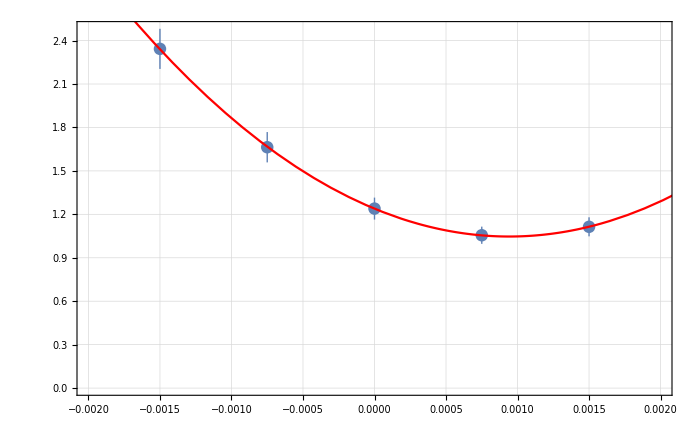
{{{2.34276×10^-9,1.66342×10^-9,1.23963×10^-9,1.05561×10^-9,1.11381×10^-9},{1.38606×10^-10,1.04754×10^-10,7.57989×10^-11,5.94018×10^-11,6.56705×10^-11}},b0 =  | 0.00094175
FittedModel[1.04677×10^-9+0.00021685 (-0.00094175+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | 0.00094175 | 0.000167658 | 5.61709 | 0.0302627
scale | 0.00021685 | 0.0000415438 | 5.2198 | 0.0347978
yoffset | 1.04677×10^-9 | 4.1007×10^-11 | 25.5266 | 0.00153115 | 
 | DF | SS | MS
Model | 3 | 1408.76 | 469.585
Error | 2 | 0.00227456 | 0.00113728
Uncorrected Total | 5 | 1408.76 | 
Corrected Total | 4 | 92.7159 |  | ,-Graphics-}

```mathematica
AlphaInvest=TransferToRefParableFit[RefSpectrum[[All,2]],AlphaDataList,bList, 4]
```

```mathematica
AlphaInvest[[2,1,1,2]]/(5*10^-5)
```

18.835

# drRxB, 9.06

```mathematica
dParameter="rRxB";
```

### b=0

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_d"<>dParameter<>"/b0/"];
```

```mathematica
dAlphaSubFileNamesb0=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_D_BSOn_drRxB_b0_1-98.txt,TransferResult_08-09-20_NC_opt_D_BSOn_drRxB_b0_99-106.txt,TransferResult_08-09-20_NC_opt_D_BSOn_drRxB_b0_107-122.txt,TransferResult_08-09-20_NC_opt_D_BSOn_drRxB_b0_123-138.txt,TransferResult_08-09-20_NC_opt_D_BSOn_drRxB_b0_139-154.txt,TransferResult_08-09-20_NC_opt_D_BSOn_drRxB_b0_155-170.txt,TransferResult_08-09-20_NC_opt_D_BSOn_drRxB_b0_171-253.txt}

```mathematica
dAlphaSpectrumb0=Flatten[Import[#,"Table"]&/@dAlphaSubFileNamesb0,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb0[[All,2]]}],PlotRange->All]*)
```

### b=15

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_d"<>dParameter<>"/b15/"];
```

```mathematica
dAlphaSubFileNamesb15=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_G_BSOn_drRxB_b15_1-98.txt,TransferResult_08-09-20_NC_opt_G_BSOn_drRxB_b15_99-106.txt,TransferResult_08-09-20_NC_opt_G_BSOn_drRxB_b15_107-122.txt,TransferResult_08-09-20_NC_opt_G_BSOn_drRxB_b15_123-138.txt,TransferResult_08-09-20_NC_opt_G_BSOn_drRxB_b15_139-154.txt,TransferResult_08-09-20_NC_opt_G_BSOn_drRxB_b15_155-170.txt,TransferResult_08-09-20_NC_opt_G_BSOn_drRxB_b15_171-253.txt}

```mathematica
dAlphaSpectrumb15=Flatten[Import[#,"Table"]&/@dAlphaSubFileNamesb15,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumb0[[All,2]]}],PlotRange->All]*)
```

### b=7.5

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_d"<>dParameter<>"/b7/"];
```

```mathematica
dAlphaSubFileNamesb75=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_C_BSOn_drRxB_b7_1-98.txt,TransferResult_08-09-20_NC_opt_C_BSOn_drRxB_b7_99-106.txt,TransferResult_08-09-20_NC_opt_C_BSOn_drRxB_b7_107-122.txt,TransferResult_08-09-20_NC_opt_C_BSOn_drRxB_b7_123-138.txt,TransferResult_08-09-20_NC_opt_C_BSOn_drRxB_b7_139-154.txt,TransferResult_08-09-20_NC_opt_C_BSOn_drRxB_b7_155-170.txt,TransferResult_08-09-20_NC_opt_C_BSOn_drRxB_b7_171-253.txt}

```mathematica
dAlphaSpectrumb75=Flatten[Import[#,"Table"]&/@dAlphaSubFileNamesb75,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumb75[[All,2]]}],PlotRange->All]*)
```

### b=-7.5

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_d"<>dParameter<>"/b-7/"];
```

```mathematica
dAlphaSubFileNamesbm75=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_C_BSOn_drRxB_b-7_1-98.txt,TransferResult_08-09-20_NC_opt_C_BSOn_drRxB_b-7_99-106.txt,TransferResult_08-09-20_NC_opt_C_BSOn_drRxB_b-7_107-122.txt,TransferResult_08-09-20_NC_opt_C_BSOn_drRxB_b-7_123-138.txt,TransferResult_08-09-20_NC_opt_C_BSOn_drRxB_b-7_139-154.txt,TransferResult_08-09-20_NC_opt_C_BSOn_drRxB_b-7_155-170.txt,TransferResult_08-09-20_NC_opt_C_BSOn_drRxB_b-7_171-253.txt}

```mathematica
dAlphaSpectrumbm75=Flatten[Import[#,"Table"]&/@dAlphaSubFileNamesbm75,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumbm75[[All,2]]}],PlotRange->All]*)
```

### b=-15

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_d"<>dParameter<>"/b-15/"];
```

```mathematica
dAlphaSubFileNamesbm15=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_C_BSOn_drRxB_b-15_1-98.txt,TransferResult_08-09-20_NC_opt_C_BSOn_drRxB_b-15_99-106.txt,TransferResult_08-09-20_NC_opt_C_BSOn_drRxB_b-15_107-122.txt,TransferResult_08-09-20_NC_opt_C_BSOn_drRxB_b-15_123-138.txt,TransferResult_08-09-20_NC_opt_C_BSOn_drRxB_b-15_139-154.txt,TransferResult_08-09-20_NC_opt_C_BSOn_drRxB_b-15_155-170.txt,TransferResult_08-09-20_NC_opt_C_BSOn_drRxB_b-15_171-253.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
dAlphaSpectrumbm15=Flatten[Import[#,"Table"]&/@dAlphaSubFileNamesbm15,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumbm15[[All,2]]}],PlotRange->All]
```

-Graphics3D-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFit]
```

```mathematica
Get["Common/CommonFunctions.m"]
```

```mathematica
AlphaDataList={dAlphaSpectrumbm15[[All,2]]/Total[dAlphaSpectrumbm15[[All,2]]],dAlphaSpectrumbm75[[All,2]]/Total[dAlphaSpectrumbm75[[All,2]]],dAlphaSpectrumb0[[All,2]]/Total[dAlphaSpectrumb0[[All,2]]],dAlphaSpectrumb75[[All,2]]/Total[dAlphaSpectrumb75[[All,2]]],dAlphaSpectrumb15[[All,2]]/Total[dAlphaSpectrumb15[[All,2]]]};
```

```mathematica
bList={-15,-7.5,0.,7.5,15}*10^-4.
```

{-0.0015,-0.00075,0.,0.00075,0.0015}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

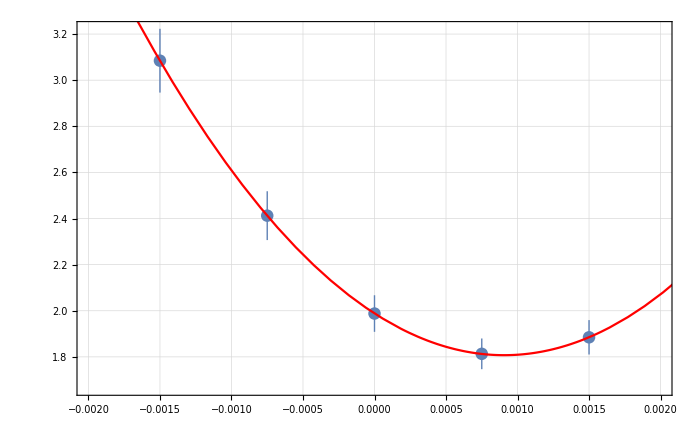
{{{3.08457×10^-9,2.41243×10^-9,1.98788×10^-9,1.81313×10^-9,1.88483×10^-9},{1.38357×10^-10,1.05884×10^-10,7.93286×10^-11,6.65689×10^-11,7.45879×10^-11}},b0 =  | 0.000906202
FittedModel[1.80731×10^-9+0.000220557 (-0.000906202+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | 0.000906202 | 0.000174718 | 5.18666 | 0.0352206
scale | 0.000220557 | 0.0000440966 | 5.00168 | 0.0377257
yoffset | 1.80731×10^-9 | 4.53205×10^-11 | 39.8783 | 0.000628228 | 
 | DF | SS | MS
Model | 3 | 3024.49 | 1008.16
Error | 2 | 0.000108929 | 0.0000544644
Uncorrected Total | 5 | 3024.49 | 
Corrected Total | 4 | 85.7455 |  | ,-Graphics-}

```mathematica
AlphaInvest=TransferToRefParableFit[RefSpectrum[[All,2]],AlphaDataList,bList, 4]
```

```mathematica
AlphaInvest[[2,1,1,2]]/(10^-4)
```

9.06202

# drF, 0.979

```mathematica
dParameter="rF";
```

### b=0

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_d"<>dParameter<>"/b0/"];
```

```mathematica
dAlphaSubFileNamesb0=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_C_BSOn_drF_b0_1-98.txt,TransferResult_08-09-20_NC_opt_C_BSOn_drF_b0_99-106.txt,TransferResult_08-09-20_NC_opt_C_BSOn_drF_b0_107-122.txt,TransferResult_08-09-20_NC_opt_C_BSOn_drF_b0_123-138.txt,TransferResult_08-09-20_NC_opt_C_BSOn_drF_b0_139-154.txt,TransferResult_08-09-20_NC_opt_C_BSOn_drF_b0_155-178.txt,TransferResult_08-09-20_NC_opt_C_BSOn_drF_b0_179-253.txt}

```mathematica
dAlphaSpectrumb0=Flatten[Import[#,"Table"]&/@dAlphaSubFileNamesb0,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb0[[All,2]]}],PlotRange->All]*)
```

### b=15

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_d"<>dParameter<>"/b15/"];
```

```mathematica
dAlphaSubFileNamesb15=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_G_BSOn_drF_b15_1-98.txt,TransferResult_08-09-20_NC_opt_G_BSOn_drF_b15_99-106.txt,TransferResult_08-09-20_NC_opt_G_BSOn_drF_b15_107-122.txt,TransferResult_08-09-20_NC_opt_G_BSOn_drF_b15_123-138.txt,TransferResult_08-09-20_NC_opt_G_BSOn_drF_b15_139-154.txt,TransferResult_08-09-20_NC_opt_G_BSOn_drF_b15_155-178.txt,TransferResult_08-09-20_NC_opt_G_BSOn_drF_b15_179-253.txt}

```mathematica
dAlphaSpectrumb15=Flatten[Import[#,"Table"]&/@dAlphaSubFileNamesb15,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumb0[[All,2]]}],PlotRange->All]*)
```

### b=7.5

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_d"<>dParameter<>"/b7/"];
```

```mathematica
dAlphaSubFileNamesb75=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_C_BSOn_drF_b7_1-98.txt,TransferResult_08-09-20_NC_opt_C_BSOn_drF_b7_99-106.txt,TransferResult_08-09-20_NC_opt_C_BSOn_drF_b7_107-122.txt,TransferResult_08-09-20_NC_opt_C_BSOn_drF_b7_123-138.txt,TransferResult_08-09-20_NC_opt_C_BSOn_drF_b7_139-154.txt,TransferResult_08-09-20_NC_opt_C_BSOn_drF_b7_155-178.txt,TransferResult_08-09-20_NC_opt_C_BSOn_drF_b7_179-253.txt}

```mathematica
dAlphaSpectrumb75=Flatten[Import[#,"Table"]&/@dAlphaSubFileNamesb75,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumb75[[All,2]]}],PlotRange->All]*)
```

### b=-7.5

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_d"<>dParameter<>"/b-7/"];
```

```mathematica
dAlphaSubFileNamesbm75=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_C_BSOn_drF_b-7_1-98.txt,TransferResult_08-09-20_NC_opt_C_BSOn_drF_b-7_99-106.txt,TransferResult_08-09-20_NC_opt_C_BSOn_drF_b-7_107-122.txt,TransferResult_08-09-20_NC_opt_C_BSOn_drF_b-7_123-138.txt,TransferResult_08-09-20_NC_opt_C_BSOn_drF_b-7_139-154.txt,TransferResult_08-09-20_NC_opt_C_BSOn_drF_b-7_155-178.txt,TransferResult_08-09-20_NC_opt_C_BSOn_drF_b-7_179-253.txt}

```mathematica
dAlphaSpectrumbm75=Flatten[Import[#,"Table"]&/@dAlphaSubFileNamesbm75,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumbm75[[All,2]]}],PlotRange->All]*)
```

### b=-15

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_d"<>dParameter<>"/b-15/"];
```

```mathematica
dAlphaSubFileNamesbm15=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_G_BSOn_drF_b-15_1-98.txt,TransferResult_08-09-20_NC_opt_G_BSOn_drF_b-15_99-106.txt,TransferResult_08-09-20_NC_opt_G_BSOn_drF_b-15_107-122.txt,TransferResult_08-09-20_NC_opt_G_BSOn_drF_b-15_123-138.txt,TransferResult_08-09-20_NC_opt_G_BSOn_drF_b-15_139-154.txt,TransferResult_08-09-20_NC_opt_G_BSOn_drF_b-15_155-178.txt,TransferResult_08-09-20_NC_opt_G_BSOn_drF_b-15_179-253.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
dAlphaSpectrumbm15=Flatten[Import[#,"Table"]&/@dAlphaSubFileNamesbm15,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumbm15[[All,2]]}],PlotRange->All]
```

-Graphics3D-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFit]
```

```mathematica
Get["Common/CommonFunctions.m"]
```

```mathematica
AlphaDataList={dAlphaSpectrumbm15[[All,2]]/Total[dAlphaSpectrumbm15[[All,2]]],dAlphaSpectrumbm75[[All,2]]/Total[dAlphaSpectrumbm75[[All,2]]],dAlphaSpectrumb0[[All,2]]/Total[dAlphaSpectrumb0[[All,2]]],dAlphaSpectrumb75[[All,2]]/Total[dAlphaSpectrumb75[[All,2]]],dAlphaSpectrumb15[[All,2]]/Total[dAlphaSpectrumb15[[All,2]]]};
```

```mathematica
bList={-15,-7.5,0.,7.5,15}*10^-4.
```

{-0.0015,-0.00075,0.,0.00075,0.0015}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

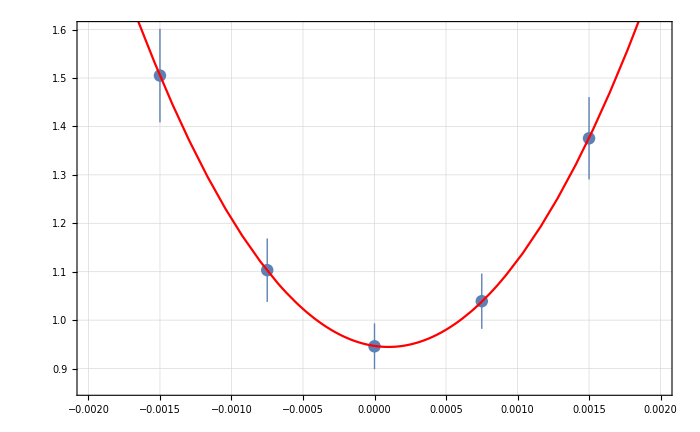
{{{1.505×10^-9,1.10318×10^-9,9.45955×10^-10,1.03911×10^-9,1.37547×10^-9},{9.66052×10^-11,6.54835×10^-11,4.72395×10^-11,5.71237×10^-11,8.49936×10^-11}},b0 =  | 0.0000978928
FittedModel[9.44676×10^-10+0.000219522 (-0.0000978928+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | 0.0000978928 | 0.0000787959 | 1.24236 | 0.340016
scale | 0.000219522 | 0.0000350361 | 6.2656 | 0.024539
yoffset | 9.44676×10^-10 | 3.726×10^-11 | 25.3536 | 0.00155205 | 
 | DF | SS | MS
Model | 3 | 1520.3 | 506.766
Error | 2 | 0.000861846 | 0.000430923
Uncorrected Total | 5 | 1520.3 | 
Corrected Total | 4 | 39.8288 |  | ,-Graphics-}

```mathematica
AlphaInvest=TransferToRefParableFit[RefSpectrum[[All,2]],AlphaDataList,bList, 4]
```

```mathematica
AlphaInvest[[2,1,1,2]]/(10^-4)
```

0.978928

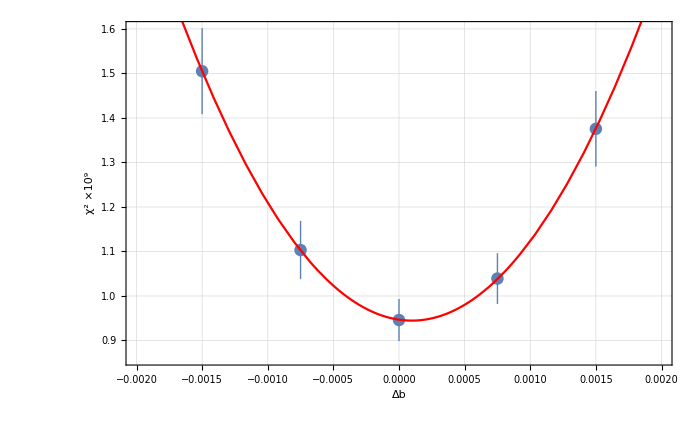

```mathematica
rFFit=Show[AlphaInvest[[3]],FrameLabel->{{"χ^2 ×10^9",None},{"Δb","Fit with deviation Δr_F/r_F = 1×10^-4"}}]
```

```mathematica
(*Export["~/Dropbox/PhD/PhDLatex/Figures/FitPlot_rF.png",rFFit,ImageResolution->450];*)
```

### check difference in drift distance spectrum

```mathematica
InterOrder=1;
```

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}],InterpolationOrder->InterOrder];
```

```mathematica
dAlphaSpectrumb0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumb0[[All,2]]/Total[dAlphaSpectrumb0[[All,2]]]}],InterpolationOrder->InterOrder];dAlphaSpectrumb75Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumb75[[All,2]]/Total[dAlphaSpectrumb75[[All,2]]]}],InterpolationOrder->InterOrder];
dAlphaSpectrumbm75Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumbm75[[All,2]]/Total[dAlphaSpectrumbm75[[All,2]]]}],InterpolationOrder->InterOrder];
dAlphaSpectrumb15Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumb15[[All,2]]/Total[dAlphaSpectrumb15[[All,2]]]}],InterpolationOrder->InterOrder];
dAlphaSpectrumbm15Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumbm15[[All,2]]/Total[dAlphaSpectrumbm15[[All,2]]]}],InterpolationOrder->InterOrder];
```

```mathematica
Plot3D[RefSpectrumInter[x,y]-dAlphaSpectrumb15Inter[x,y],{x,-0.04,0.04},{y,-0.05,0.05},PlotRange->All]
```

-Graphics3D-

```mathematica
ytest=0.0;
```

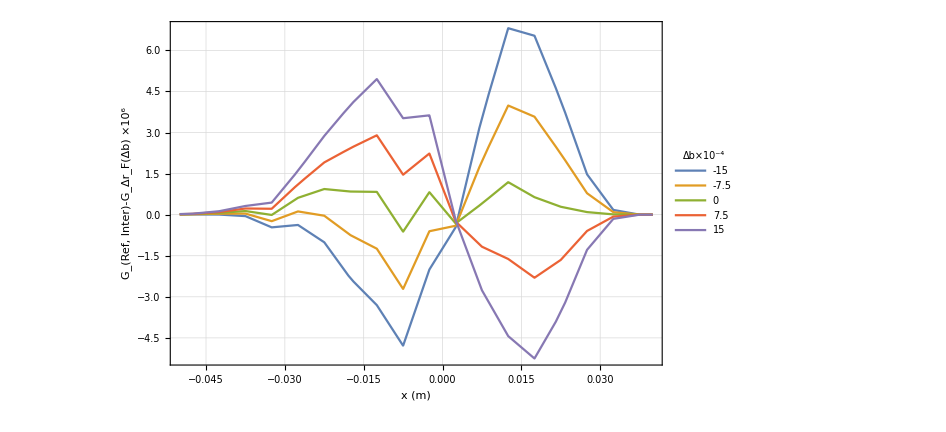

```mathematica
DeltaGxdbPlot=Plot[{
10^6*(RefSpectrumInter[x,ytest]-dAlphaSpectrumbm15Inter[x,ytest]),
10^6*(RefSpectrumInter[x,ytest]-dAlphaSpectrumbm75Inter[x,ytest]),
10^6*(RefSpectrumInter[x,ytest]-dAlphaSpectrumb0Inter[x,ytest]),
10^6*(RefSpectrumInter[x,ytest]-dAlphaSpectrumb75Inter[x,ytest]),
10^6*(RefSpectrumInter[x,ytest]-dAlphaSpectrumb15Inter[x,ytest])
}
,{x,-0.05,0.04},PlotRange->All,ImageSize->700,BaseStyle->25,FrameLabel->{{"G_(Ref, Inter)-G_Δr_F(Δb) ×10^6",None},{"x (m)","Difference in drift distance spectra by deviation Δr_F/r_F=1×10^-4"}},PlotLegends->Placed[LineLegend[{"-15","-7.5","0","7.5","15"},LegendLabel->"Δb×10^-4",LabelStyle->25,LegendFunction->(Framed[#1, FrameMargins -> 0,Background->Directive[Opacity[1],White]] & )],{0.1,0.65}]]
```

```mathematica
(*Export["~/Dropbox/PhD/PhDLatex/Figures/DeltaGxdb.png",DeltaGxdbPlot,ImageResolution->450];*)
```

# drA, -6.93

```mathematica
dParameter="rA";
```

### b=0

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_d"<>dParameter<>"/b0/"];
```

```mathematica
dAlphaSubFileNamesb0=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_D_BSOn_drA_b0_1-98.txt,TransferResult_08-09-20_NC_opt_D_BSOn_drA_b0_99-106.txt,TransferResult_08-09-20_NC_opt_D_BSOn_drA_b0_107-122.txt,TransferResult_08-09-20_NC_opt_D_BSOn_drA_b0_123-138.txt,TransferResult_08-09-20_NC_opt_D_BSOn_drA_b0_139-154.txt,TransferResult_08-09-20_NC_opt_D_BSOn_drA_b0_155-178.txt,TransferResult_08-09-20_NC_opt_D_BSOn_drA_b0_179-253.txt}

```mathematica
dAlphaSpectrumb0=Flatten[Import[#,"Table"]&/@dAlphaSubFileNamesb0,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb0[[All,2]]}],PlotRange->All]*)
```

### b=15

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_d"<>dParameter<>"/b15/"];
```

```mathematica
dAlphaSubFileNamesb15=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_G_BSOn_drA_b15_1-98.txt,TransferResult_08-09-20_NC_opt_G_BSOn_drA_b15_99-106.txt,TransferResult_08-09-20_NC_opt_G_BSOn_drA_b15_107-122.txt,TransferResult_08-09-20_NC_opt_G_BSOn_drA_b15_123-138.txt,TransferResult_08-09-20_NC_opt_G_BSOn_drA_b15_139-154.txt,TransferResult_08-09-20_NC_opt_G_BSOn_drA_b15_155-178.txt,TransferResult_08-09-20_NC_opt_G_BSOn_drA_b15_179-253.txt}

```mathematica
dAlphaSpectrumb15=Flatten[Import[#,"Table"]&/@dAlphaSubFileNamesb15,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumb0[[All,2]]}],PlotRange->All]*)
```

### b=7.5

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_d"<>dParameter<>"/b7/"];
```

```mathematica
dAlphaSubFileNamesb75=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_C_BSOn_drA_b7_1-98.txt,TransferResult_08-09-20_NC_opt_C_BSOn_drA_b7_99-106.txt,TransferResult_08-09-20_NC_opt_C_BSOn_drA_b7_107-122.txt,TransferResult_08-09-20_NC_opt_C_BSOn_drA_b7_123-138.txt,TransferResult_08-09-20_NC_opt_C_BSOn_drA_b7_139-154.txt,TransferResult_08-09-20_NC_opt_C_BSOn_drA_b7_155-178.txt,TransferResult_08-09-20_NC_opt_C_BSOn_drA_b7_179-253.txt}

```mathematica
dAlphaSpectrumb75=Flatten[Import[#,"Table"]&/@dAlphaSubFileNamesb75,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumb75[[All,2]]}],PlotRange->All]*)
```

### b=-7.5

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_d"<>dParameter<>"/b-7/"];
```

```mathematica
dAlphaSubFileNamesbm75=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_D_BSOn_drA_b-7_1-98.txt,TransferResult_08-09-20_NC_opt_D_BSOn_drA_b-7_99-106.txt,TransferResult_08-09-20_NC_opt_D_BSOn_drA_b-7_107-122.txt,TransferResult_08-09-20_NC_opt_D_BSOn_drA_b-7_123-138.txt,TransferResult_08-09-20_NC_opt_D_BSOn_drA_b-7_139-154.txt,TransferResult_08-09-20_NC_opt_D_BSOn_drA_b-7_155-178.txt,TransferResult_08-09-20_NC_opt_D_BSOn_drA_b-7_179-253.txt}

```mathematica
dAlphaSpectrumbm75=Flatten[Import[#,"Table"]&/@dAlphaSubFileNamesbm75,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumbm75[[All,2]]}],PlotRange->All]*)
```

### b=-15

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_d"<>dParameter<>"/b-15/"];
```

```mathematica
dAlphaSubFileNamesbm15=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_G_BSOn_drA_b-15_1-98.txt,TransferResult_08-09-20_NC_opt_G_BSOn_drA_b-15_99-106.txt,TransferResult_08-09-20_NC_opt_G_BSOn_drA_b-15_107-122.txt,TransferResult_08-09-20_NC_opt_G_BSOn_drA_b-15_123-138.txt,TransferResult_08-09-20_NC_opt_G_BSOn_drA_b-15_139-154.txt,TransferResult_08-09-20_NC_opt_G_BSOn_drA_b-15_155-178.txt,TransferResult_08-09-20_NC_opt_G_BSOn_drA_b-15_179-253.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
dAlphaSpectrumbm15=Flatten[Import[#,"Table"]&/@dAlphaSubFileNamesbm15,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumbm15[[All,2]]}],PlotRange->All]
```

-Graphics3D-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFit]
```

```mathematica
Get["Common/CommonFunctions.m"]
```

```mathematica
AlphaDataList={dAlphaSpectrumbm15[[All,2]]/Total[dAlphaSpectrumbm15[[All,2]]],dAlphaSpectrumbm75[[All,2]]/Total[dAlphaSpectrumbm75[[All,2]]],dAlphaSpectrumb0[[All,2]]/Total[dAlphaSpectrumb0[[All,2]]],dAlphaSpectrumb75[[All,2]]/Total[dAlphaSpectrumb75[[All,2]]],dAlphaSpectrumb15[[All,2]]/Total[dAlphaSpectrumb15[[All,2]]]};
```

```mathematica
bList={-15,-7.5,0.,7.5,15}*10^-4.
```

{-0.0015,-0.00075,0.,0.00075,0.0015}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

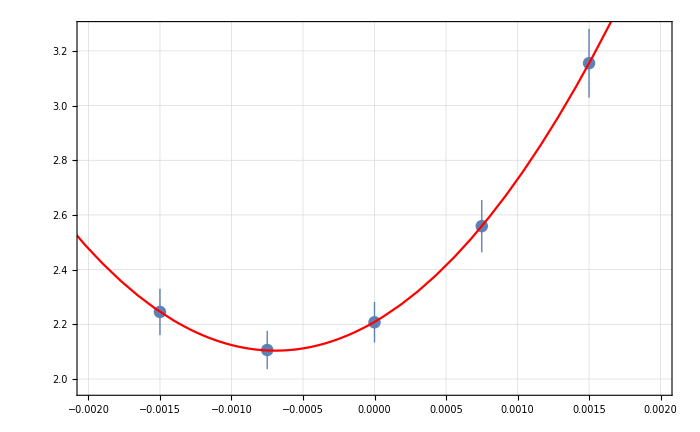
{{{2.24511×10^-9,2.10593×10^-9,2.20735×10^-9,2.55907×10^-9,3.15517×10^-9},{8.47816×10^-11,7.00963×10^-11,7.42199×10^-11,9.58334×10^-11,1.2583×10^-10}},b0 =  | -0.000693291
FittedModel[2.1037×10^-9+0.00021846 (0.000693291+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.000693291 | 0.00015037 | -4.61056 | 0.0439638
scale | 0.00021846 | 0.0000437366 | 4.99489 | 0.0378225
yoffset | 2.1037×10^-9 | 4.76258×10^-11 | 44.1714 | 0.000512135 | 
 | DF | SS | MS
Model | 3 | 3830.17 | 1276.72
Error | 2 | 0.000915385 | 0.000457693
Uncorrected Total | 5 | 3830.17 | 
Corrected Total | 4 | 62.6597 |  | ,-Graphics-}

```mathematica
AlphaInvest=TransferToRefParableFit[RefSpectrum[[All,2]],AlphaDataList,bList, 4]
```

```mathematica
AlphaInvest[[2,1,1,2]]/(10^-4)
```

-6.93291

### check difference in drift distance spectrum

```mathematica
InterOrder=1;
```

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}],InterpolationOrder->InterOrder];
```

```mathematica
dAlphaSpectrumb0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumb0[[All,2]]/Total[dAlphaSpectrumb0[[All,2]]]}],InterpolationOrder->InterOrder];dAlphaSpectrumb75Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumb75[[All,2]]/Total[dAlphaSpectrumb75[[All,2]]]}],InterpolationOrder->InterOrder];
dAlphaSpectrumbm75Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumbm75[[All,2]]/Total[dAlphaSpectrumbm75[[All,2]]]}],InterpolationOrder->InterOrder];
dAlphaSpectrumb15Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumb15[[All,2]]/Total[dAlphaSpectrumb15[[All,2]]]}],InterpolationOrder->InterOrder];
dAlphaSpectrumbm15Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumbm15[[All,2]]/Total[dAlphaSpectrumbm15[[All,2]]]}],InterpolationOrder->InterOrder];
```

```mathematica
Plot3D[RefSpectrumInter[x,y]-dAlphaSpectrumb15Inter[x,y],{x,-0.04,0.04},{y,-0.05,0.05},PlotRange->All]
```

-Graphics3D-

```mathematica
ytest=0.0;
```

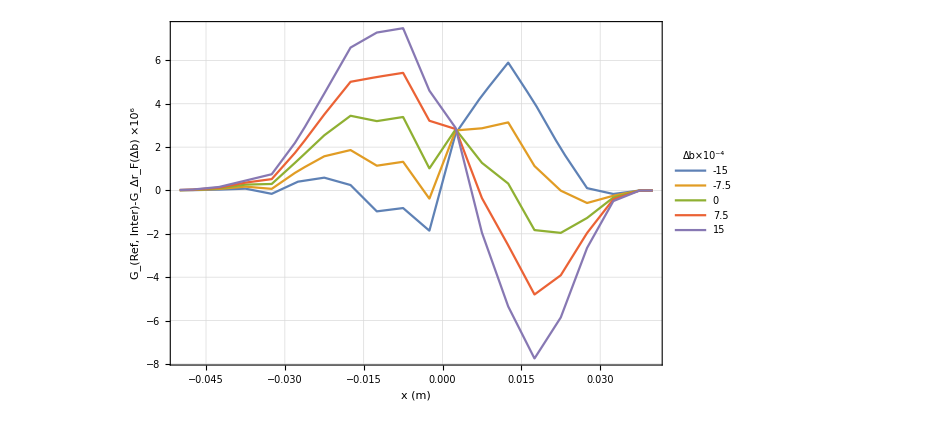

```mathematica
DeltaGxdbPlot=Plot[{
10^6*(RefSpectrumInter[x,ytest]-dAlphaSpectrumbm15Inter[x,ytest]),
10^6*(RefSpectrumInter[x,ytest]-dAlphaSpectrumbm75Inter[x,ytest]),
10^6*(RefSpectrumInter[x,ytest]-dAlphaSpectrumb0Inter[x,ytest]),
10^6*(RefSpectrumInter[x,ytest]-dAlphaSpectrumb75Inter[x,ytest]),
10^6*(RefSpectrumInter[x,ytest]-dAlphaSpectrumb15Inter[x,ytest])
}
,{x,-0.05,0.04},PlotRange->All,ImageSize->700,BaseStyle->25,FrameLabel->{{"G_(Ref, Inter)-G_Δr_F(Δb) ×10^6",None},{"x (m)","Difference in drift distance spectra by deviation Δr_F/r_F=1×10^-4"}},PlotLegends->Placed[LineLegend[{"-15","-7.5","0","7.5","15"},LegendLabel->"Δb×10^-4",LabelStyle->25,LegendFunction->(Framed[#1, FrameMargins -> 0,Background->Directive[Opacity[1],White]] & )],{0.1,0.65}]]
```

```mathematica
(*Export["~/Dropbox/PhD/PhDLatex/Figures/DeltaGxdb.png",DeltaGxdbPlot,ImageResolution->450];*)
```

# drD, 2.13

```mathematica
dParameter="rD";
```

### b=0

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_d"<>dParameter<>"/b0/"];
```

```mathematica
dAlphaSubFileNamesb0=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_H_BSOn_drD_b0_1-98.txt,TransferResult_08-09-20_NC_opt_H_BSOn_drD_b0_99-106.txt,TransferResult_08-09-20_NC_opt_H_BSOn_drD_b0_107-122.txt,TransferResult_08-09-20_NC_opt_H_BSOn_drD_b0_123-138.txt,TransferResult_08-09-20_NC_opt_H_BSOn_drD_b0_139-154.txt,TransferResult_08-09-20_NC_opt_H_BSOn_drD_b0_155-178.txt,TransferResult_08-09-20_NC_opt_H_BSOn_drD_b0_179-253.txt}

```mathematica
dAlphaSpectrumb0=Flatten[Import[#,"Table"]&/@dAlphaSubFileNamesb0,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb0[[All,2]]}],PlotRange->All]*)
```

### b=15

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_d"<>dParameter<>"/b15/"];
```

```mathematica
dAlphaSubFileNamesb15=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_G_BSOn_drD_b15_1-98.txt,TransferResult_08-09-20_NC_opt_G_BSOn_drD_b15_99-106.txt,TransferResult_08-09-20_NC_opt_G_BSOn_drD_b15_107-122.txt,TransferResult_08-09-20_NC_opt_G_BSOn_drD_b15_123-138.txt,TransferResult_08-09-20_NC_opt_G_BSOn_drD_b15_139-154.txt,TransferResult_08-09-20_NC_opt_G_BSOn_drD_b15_155-178.txt,TransferResult_08-09-20_NC_opt_G_BSOn_drD_b15_179-253.txt}

```mathematica
dAlphaSpectrumb15=Flatten[Import[#,"Table"]&/@dAlphaSubFileNamesb15,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumb0[[All,2]]}],PlotRange->All]*)
```

### b=7.5

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_d"<>dParameter<>"/b7/"];
```

```mathematica
dAlphaSubFileNamesb75=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_C_BSOn_drD_b7_1-98.txt,TransferResult_08-09-20_NC_opt_H_BSOn_drD_b7_99-106.txt,TransferResult_08-09-20_NC_opt_C_BSOn_drD_b7_107-122.txt,TransferResult_08-09-20_NC_opt_C_BSOn_drD_b7_123-138.txt,TransferResult_08-09-20_NC_opt_C_BSOn_drD_b7_139-154.txt,TransferResult_08-09-20_NC_opt_C_BSOn_drD_b7_155-178.txt,TransferResult_08-09-20_NC_opt_C_BSOn_drD_b7_179-253.txt}

```mathematica
dAlphaSpectrumb75=Flatten[Import[#,"Table"]&/@dAlphaSubFileNamesb75,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumb75[[All,2]]}],PlotRange->All]*)
```

### b=-7.5

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_d"<>dParameter<>"/b-7/"];
```

```mathematica
dAlphaSubFileNamesbm75=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_D_BSOn_drD_b-7_1-98.txt,TransferResult_08-09-20_NC_opt_D_BSOn_drD_b-7_99-106.txt,TransferResult_08-09-20_NC_opt_D_BSOn_drD_b-7_107-122.txt,TransferResult_08-09-20_NC_opt_D_BSOn_drD_b-7_123-138.txt,TransferResult_08-09-20_NC_opt_H_BSOn_drD_b-7_139-154.txt,TransferResult_08-09-20_NC_opt_D_BSOn_drD_b-7_155-178.txt,TransferResult_08-09-20_NC_opt_D_BSOn_drD_b-7_179-253.txt}

```mathematica
dAlphaSpectrumbm75=Flatten[Import[#,"Table"]&/@dAlphaSubFileNamesbm75,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumbm75[[All,2]]}],PlotRange->All]*)
```

### b=-15

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_d"<>dParameter<>"/b-15/"];
```

```mathematica
dAlphaSubFileNamesbm15=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_G_BSOn_drD_b-15_1-98.txt,TransferResult_08-09-20_NC_opt_G_BSOn_drD_b-15_99-106.txt,TransferResult_08-09-20_NC_opt_G_BSOn_drD_b-15_107-122.txt,TransferResult_08-09-20_NC_opt_G_BSOn_drD_b-15_123-138.txt,TransferResult_08-09-20_NC_opt_G_BSOn_drD_b-15_139-154.txt,TransferResult_08-09-20_NC_opt_G_BSOn_drD_b-15_155-178.txt,TransferResult_08-09-20_NC_opt_G_BSOn_drD_b-15_179-253.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
dAlphaSpectrumbm15=Flatten[Import[#,"Table"]&/@dAlphaSubFileNamesbm15,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumbm15[[All,2]]}],PlotRange->All]
```

-Graphics3D-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFit]
```

```mathematica
Get["Common/CommonFunctions.m"]
```

```mathematica
AlphaDataList={dAlphaSpectrumbm15[[All,2]]/Total[dAlphaSpectrumbm15[[All,2]]],dAlphaSpectrumbm75[[All,2]]/Total[dAlphaSpectrumbm75[[All,2]]],dAlphaSpectrumb0[[All,2]]/Total[dAlphaSpectrumb0[[All,2]]],dAlphaSpectrumb75[[All,2]]/Total[dAlphaSpectrumb75[[All,2]]],dAlphaSpectrumb15[[All,2]]/Total[dAlphaSpectrumb15[[All,2]]]};
```

```mathematica
bList={-15,-7.5,0.,7.5,15}*10^-4.
```

{-0.0015,-0.00075,0.,0.00075,0.0015}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

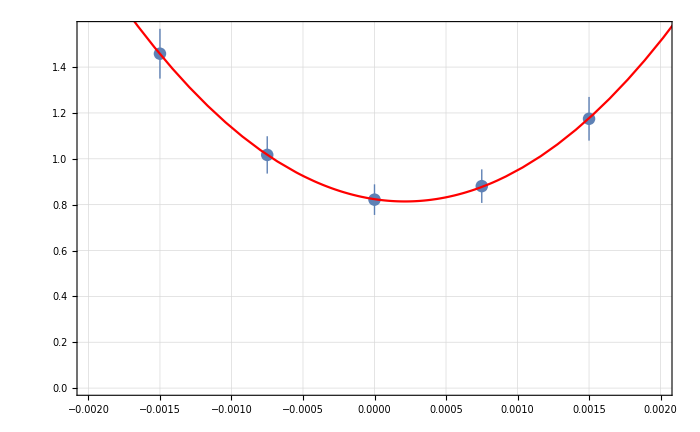
{{{1.4584×10^-9,1.01696×10^-9,8.21913×10^-10,8.80751×10^-10,1.17452×10^-9},{1.08611×10^-10,8.14103×10^-11,6.66802×10^-11,7.32019×10^-11,9.52655×10^-11}},b0 =  | 0.000213186
FittedModel[8.14007×10^-10+0.000219133 (-0.000213186+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | 0.000213186 | 0.0000973924 | 2.18894 | 0.160052
scale | 0.000219133 | 0.0000419346 | 5.22559 | 0.0347247
yoffset | 8.14007×10^-10 | 4.9549×10^-11 | 16.4283 | 0.00368475 | 
 | DF | SS | MS
Model | 3 | 785.045 | 261.682
Error | 2 | 0.00411815 | 0.00205907
Uncorrected Total | 5 | 785.049 | 
Corrected Total | 4 | 30.9956 |  | ,-Graphics-}

```mathematica
AlphaInvest=TransferToRefParableFit[RefSpectrum[[All,2]],AlphaDataList,bList, 4]
```

```mathematica
AlphaInvest[[2,1,1,2]]/(10^-4)
```

2.13186

### check difference in drift distance spectrum

```mathematica
InterOrder=1;
```

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}],InterpolationOrder->InterOrder];
```

```mathematica
dAlphaSpectrumb0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumb0[[All,2]]/Total[dAlphaSpectrumb0[[All,2]]]}],InterpolationOrder->InterOrder];dAlphaSpectrumb75Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumb75[[All,2]]/Total[dAlphaSpectrumb75[[All,2]]]}],InterpolationOrder->InterOrder];
dAlphaSpectrumbm75Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumbm75[[All,2]]/Total[dAlphaSpectrumbm75[[All,2]]]}],InterpolationOrder->InterOrder];
dAlphaSpectrumb15Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumb15[[All,2]]/Total[dAlphaSpectrumb15[[All,2]]]}],InterpolationOrder->InterOrder];
dAlphaSpectrumbm15Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumbm15[[All,2]]/Total[dAlphaSpectrumbm15[[All,2]]]}],InterpolationOrder->InterOrder];
```

```mathematica
Plot3D[RefSpectrumInter[x,y]-dAlphaSpectrumb15Inter[x,y],{x,-0.04,0.04},{y,-0.05,0.05},PlotRange->All]
```

-Graphics3D-

```mathematica
ytest=0.0;
```

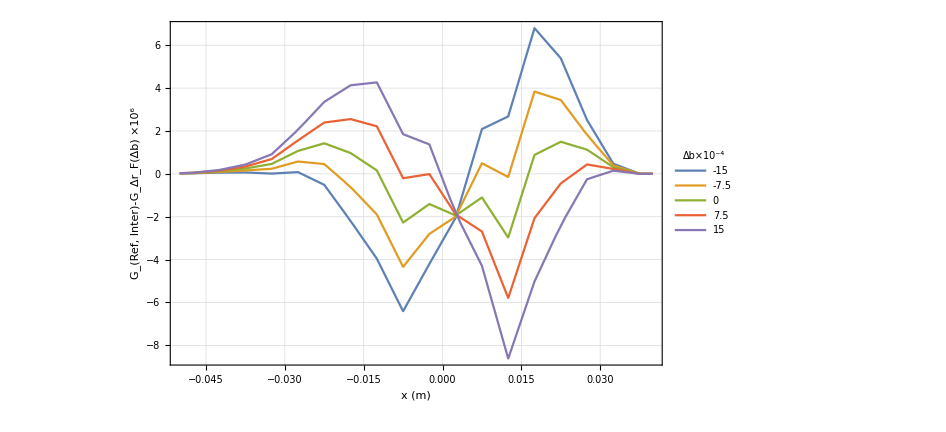

```mathematica
DeltaGxdbPlot=Plot[{
10^6*(RefSpectrumInter[x,ytest]-dAlphaSpectrumbm15Inter[x,ytest]),
10^6*(RefSpectrumInter[x,ytest]-dAlphaSpectrumbm75Inter[x,ytest]),
10^6*(RefSpectrumInter[x,ytest]-dAlphaSpectrumb0Inter[x,ytest]),
10^6*(RefSpectrumInter[x,ytest]-dAlphaSpectrumb75Inter[x,ytest]),
10^6*(RefSpectrumInter[x,ytest]-dAlphaSpectrumb15Inter[x,ytest])
}
,{x,-0.05,0.04},PlotRange->All,ImageSize->700,BaseStyle->25,FrameLabel->{{"G_(Ref, Inter)-G_Δr_F(Δb) ×10^6",None},{"x (m)","Difference in drift distance spectra by deviation Δr_F/r_F=1×10^-4"}},PlotLegends->Placed[LineLegend[{"-15","-7.5","0","7.5","15"},LegendLabel->"Δb×10^-4",LabelStyle->25,LegendFunction->(Framed[#1, FrameMargins -> 0,Background->Directive[Opacity[1],White]] & )],{0.1,0.65}]]
```

```mathematica
(*Export["~/Dropbox/PhD/PhDLatex/Figures/DeltaGxdb.png",DeltaGxdbPlot,ImageResolution->450];*)
```

# dG1, 0.863

```mathematica
dParameter="G1";
```

### b=0

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_d"<>dParameter<>"/b0/"];
```

```mathematica
dAlphaSubFileNamesb0=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_H_BSOn_dG1_b0_1-98.txt,TransferResult_08-09-20_NC_opt_H_BSOn_dG1_b0_99-106.txt,TransferResult_08-09-20_NC_opt_H_BSOn_dG1_b0_107-122.txt,TransferResult_08-09-20_NC_opt_H_BSOn_dG1_b0_123-138.txt,TransferResult_08-09-20_NC_opt_H_BSOn_dG1_b0_139-154.txt,TransferResult_08-09-20_NC_opt_H_BSOn_dG1_b0_155-178.txt,TransferResult_08-09-20_NC_opt_H_BSOn_dG1_b0_179-253.txt}

```mathematica
dAlphaSpectrumb0=Flatten[Import[#,"Table"]&/@dAlphaSubFileNamesb0,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb0[[All,2]]}],PlotRange->All]*)
```

### b=15

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_d"<>dParameter<>"/b15/"];
```

```mathematica
dAlphaSubFileNamesb15=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_G_BSOn_dG1_b15_1-98.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dG1_b15_99-106.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dG1_b15_107-122.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dG1_b15_123-138.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dG1_b15_139-154.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dG1_b15_155-178.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dG1_b15_179-253.txt}

```mathematica
dAlphaSpectrumb15=Flatten[Import[#,"Table"]&/@dAlphaSubFileNamesb15,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumb0[[All,2]]}],PlotRange->All]*)
```

### b=7.5

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_d"<>dParameter<>"/b7/"];
```

```mathematica
dAlphaSubFileNamesb75=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_D_BSOn_dG1_b7_1-98.txt,TransferResult_08-09-20_NC_opt_D_BSOn_dG1_b7_99-106.txt,TransferResult_08-09-20_NC_opt_D_BSOn_dG1_b7_107-122.txt,TransferResult_08-09-20_NC_opt_D_BSOn_dG1_b7_123-138.txt,TransferResult_08-09-20_NC_opt_D_BSOn_dG1_b7_139-154.txt,TransferResult_08-09-20_NC_opt_D_BSOn_dG1_b7_155-178.txt,TransferResult_08-09-20_NC_opt_D_BSOn_dG1_b7_179-253.txt}

```mathematica
dAlphaSpectrumb75=Flatten[Import[#,"Table"]&/@dAlphaSubFileNamesb75,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumb75[[All,2]]}],PlotRange->All]*)
```

### b=-7.5

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_d"<>dParameter<>"/b-7/"];
```

```mathematica
dAlphaSubFileNamesbm75=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_C_BSOn_dG1_b-7_1-98.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dG1_b-7_99-106.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dG1_b-7_107-122.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dG1_b-7_123-138.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dG1_b-7_139-154.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dG1_b-7_155-178.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dG1_b-7_179-253.txt}

```mathematica
dAlphaSpectrumbm75=Flatten[Import[#,"Table"]&/@dAlphaSubFileNamesbm75,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumbm75[[All,2]]}],PlotRange->All]*)
```

### b=-15

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_d"<>dParameter<>"/b-15/"];
```

```mathematica
dAlphaSubFileNamesbm15=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_G_BSOn_dG1_b-15_1-98.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dG1_b-15_99-106.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dG1_b-15_107-122.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dG1_b-15_123-138.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dG1_b-15_139-154.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dG1_b-15_155-178.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dG1_b-15_179-253.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
dAlphaSpectrumbm15=Flatten[Import[#,"Table"]&/@dAlphaSubFileNamesbm15,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumbm15[[All,2]]}],PlotRange->All]
```

-Graphics3D-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFit]
```

```mathematica
Get["Common/CommonFunctions.m"]
```

```mathematica
AlphaDataList={dAlphaSpectrumbm15[[All,2]]/Total[dAlphaSpectrumbm15[[All,2]]],dAlphaSpectrumbm75[[All,2]]/Total[dAlphaSpectrumbm75[[All,2]]],dAlphaSpectrumb0[[All,2]]/Total[dAlphaSpectrumb0[[All,2]]],dAlphaSpectrumb75[[All,2]]/Total[dAlphaSpectrumb75[[All,2]]],dAlphaSpectrumb15[[All,2]]/Total[dAlphaSpectrumb15[[All,2]]]};
```

```mathematica
bList={-15,-7.5,0.,7.5,15}*10^-4.
```

{-0.0015,-0.00075,0.,0.00075,0.0015}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

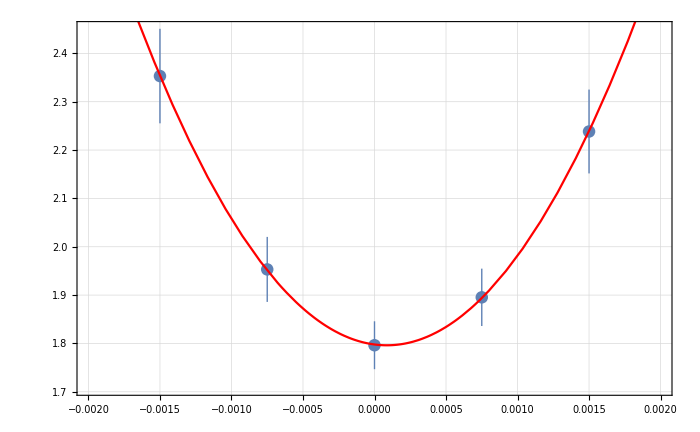
{{{2.35308×10^-9,1.95312×10^-9,1.79628×10^-9,1.89539×10^-9,2.2384×10^-9},{9.77635×10^-11,6.72304×10^-11,4.95286×10^-11,5.93222×10^-11,8.6719×10^-11}},b0 =  | 0.0000863079
FittedModel[1.79619×10^-9+0.00022169 (-0.0000863079+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | 0.0000863079 | 0.000079573 | 1.08464 | 0.391424
scale | 0.00022169 | 0.0000359027 | 6.17473 | 0.0252392
yoffset | 1.79619×10^-9 | 3.88524×10^-11 | 46.2311 | 0.000467548 | 
 | DF | SS | MS
Model | 3 | 4425.73 | 1475.24
Error | 2 | 0.00264806 | 0.00132403
Uncorrected Total | 5 | 4425.74 | 
Corrected Total | 4 | 38.535 |  | ,-Graphics-}

```mathematica
AlphaInvest=TransferToRefParableFit[RefSpectrum[[All,2]],AlphaDataList,bList, 4]
```

```mathematica
AlphaInvest[[2,1,1,2]]/(10^-4)
```

0.863079

### check difference in drift distance spectrum

```mathematica
InterOrder=1;
```

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}],InterpolationOrder->InterOrder];
```

```mathematica
dAlphaSpectrumb0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumb0[[All,2]]/Total[dAlphaSpectrumb0[[All,2]]]}],InterpolationOrder->InterOrder];dAlphaSpectrumb75Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumb75[[All,2]]/Total[dAlphaSpectrumb75[[All,2]]]}],InterpolationOrder->InterOrder];
dAlphaSpectrumbm75Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumbm75[[All,2]]/Total[dAlphaSpectrumbm75[[All,2]]]}],InterpolationOrder->InterOrder];
dAlphaSpectrumb15Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumb15[[All,2]]/Total[dAlphaSpectrumb15[[All,2]]]}],InterpolationOrder->InterOrder];
dAlphaSpectrumbm15Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumbm15[[All,2]]/Total[dAlphaSpectrumbm15[[All,2]]]}],InterpolationOrder->InterOrder];
```

```mathematica
Plot3D[RefSpectrumInter[x,y]-dAlphaSpectrumb15Inter[x,y],{x,-0.04,0.04},{y,-0.05,0.05},PlotRange->All]
```

-Graphics3D-

```mathematica
ytest=0.0;
```

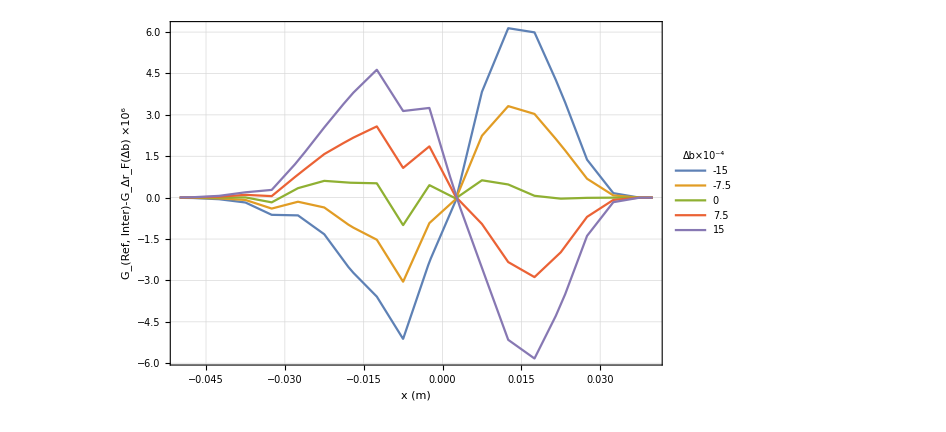

```mathematica
DeltaGxdbPlot=Plot[{
10^6*(RefSpectrumInter[x,ytest]-dAlphaSpectrumbm15Inter[x,ytest]),
10^6*(RefSpectrumInter[x,ytest]-dAlphaSpectrumbm75Inter[x,ytest]),
10^6*(RefSpectrumInter[x,ytest]-dAlphaSpectrumb0Inter[x,ytest]),
10^6*(RefSpectrumInter[x,ytest]-dAlphaSpectrumb75Inter[x,ytest]),
10^6*(RefSpectrumInter[x,ytest]-dAlphaSpectrumb15Inter[x,ytest])
}
,{x,-0.05,0.04},PlotRange->All,ImageSize->700,BaseStyle->25,FrameLabel->{{"G_(Ref, Inter)-G_Δr_F(Δb) ×10^6",None},{"x (m)","Difference in drift distance spectra by deviation Δr_F/r_F=1×10^-4"}},PlotLegends->Placed[LineLegend[{"-15","-7.5","0","7.5","15"},LegendLabel->"Δb×10^-4",LabelStyle->25,LegendFunction->(Framed[#1, FrameMargins -> 0,Background->Directive[Opacity[1],White]] & )],{0.1,0.65}]]
```

```mathematica
(*Export["~/Dropbox/PhD/PhDLatex/Figures/DeltaGxdb.png",DeltaGxdbPlot,ImageResolution->450];*)
```

# dG2, 0.950

```mathematica
dParameter="G2";
```

### b=0

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_d"<>dParameter<>"/b0/"];
```

```mathematica
dAlphaSubFileNamesb0=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_H_BSOn_dG2_b0_1-98.txt,TransferResult_08-09-20_NC_opt_H_BSOn_dG2_b0_99-106.txt,TransferResult_08-09-20_NC_opt_H_BSOn_dG2_b0_107-122.txt,TransferResult_08-09-20_NC_opt_H_BSOn_dG2_b0_123-138.txt,TransferResult_08-09-20_NC_opt_H_BSOn_dG2_b0_139-154.txt,TransferResult_08-09-20_NC_opt_H_BSOn_dG2_b0_155-178.txt,TransferResult_08-09-20_NC_opt_H_BSOn_dG2_b0_179-253.txt}

```mathematica
dAlphaSpectrumb0=Flatten[Import[#,"Table"]&/@dAlphaSubFileNamesb0,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb0[[All,2]]}],PlotRange->All]*)
```

### b=15

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_d"<>dParameter<>"/b15/"];
```

```mathematica
dAlphaSubFileNamesb15=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_G_BSOn_dG2_b15_1-98.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dG2_b15_99-106.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dG2_b15_107-122.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dG2_b15_123-138.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dG2_b15_139-154.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dG2_b15_155-178.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dG2_b15_179-253.txt}

```mathematica
dAlphaSpectrumb15=Flatten[Import[#,"Table"]&/@dAlphaSubFileNamesb15,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumb0[[All,2]]}],PlotRange->All]*)
```

### b=7.5

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_d"<>dParameter<>"/b7/"];
```

```mathematica
dAlphaSubFileNamesb75=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_C_BSOn_dG2_b7_1-98.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dG2_b7_99-106.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dG2_b7_107-122.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dG2_b7_123-138.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dG2_b7_139-154.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dG2_b7_155-178.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dG2_b7_179-253.txt}

```mathematica
dAlphaSpectrumb75=Flatten[Import[#,"Table"]&/@dAlphaSubFileNamesb75,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumb75[[All,2]]}],PlotRange->All]*)
```

### b=-7.5

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_d"<>dParameter<>"/b-7/"];
```

```mathematica
dAlphaSubFileNamesbm75=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_C_BSOn_dG2_b-7_1-98.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dG2_b-7_99-106.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dG2_b-7_107-122.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dG2_b-7_123-138.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dG2_b-7_139-154.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dG2_b-7_155-178.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dG2_b-7_179-253.txt}

```mathematica
dAlphaSpectrumbm75=Flatten[Import[#,"Table"]&/@dAlphaSubFileNamesbm75,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumbm75[[All,2]]}],PlotRange->All]*)
```

### b=-15

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_d"<>dParameter<>"/b-15/"];
```

```mathematica
dAlphaSubFileNamesbm15=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_G_BSOn_dG2_b-15_1-98.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dG2_b-15_99-106.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dG2_b-15_107-122.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dG2_b-15_123-138.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dG2_b-15_139-154.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dG2_b-15_155-178.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dG2_b-15_179-253.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
dAlphaSpectrumbm15=Flatten[Import[#,"Table"]&/@dAlphaSubFileNamesbm15,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumbm15[[All,2]]}],PlotRange->All]
```

-Graphics3D-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFit]
```

```mathematica
Get["Common/CommonFunctions.m"]
```

```mathematica
AlphaDataList={dAlphaSpectrumbm15[[All,2]]/Total[dAlphaSpectrumbm15[[All,2]]],dAlphaSpectrumbm75[[All,2]]/Total[dAlphaSpectrumbm75[[All,2]]],dAlphaSpectrumb0[[All,2]]/Total[dAlphaSpectrumb0[[All,2]]],dAlphaSpectrumb75[[All,2]]/Total[dAlphaSpectrumb75[[All,2]]],dAlphaSpectrumb15[[All,2]]/Total[dAlphaSpectrumb15[[All,2]]]};
```

```mathematica
bList={-15,-7.5,0.,7.5,15}*10^-4.
```

{-0.0015,-0.00075,0.,0.00075,0.0015}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

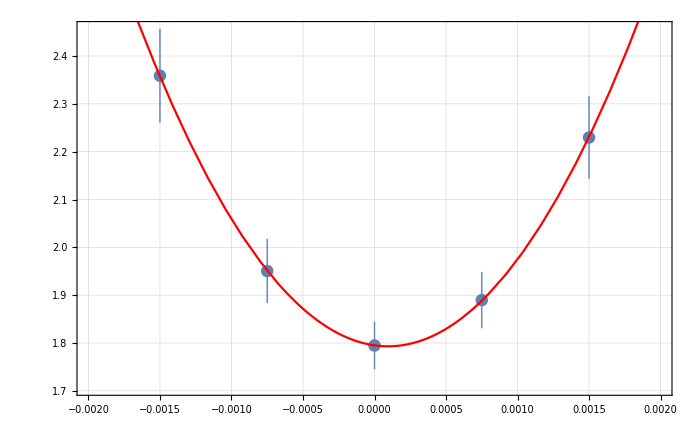
{{{2.35875×10^-9,1.95048×10^-9,1.79478×10^-9,1.88971×10^-9,2.22961×10^-9},{9.8184×10^-11,6.72161×10^-11,4.95181×10^-11,5.89651×10^-11,8.62315×10^-11}},b0 =  | 0.0000950245
FittedModel[1.79312×10^-9+0.000221813 (-0.0000950245+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | 0.0000950245 | 0.0000795105 | 1.19512 | 0.354537
scale | 0.000221813 | 0.0000358828 | 6.1816 | 0.0251852
yoffset | 1.79312×10^-9 | 3.87794×10^-11 | 46.2389 | 0.000467391 | 
 | DF | SS | MS
Model | 3 | 4428.48 | 1476.16
Error | 2 | 0.00130014 | 0.000650069
Uncorrected Total | 5 | 4428.48 | 
Corrected Total | 4 | 38.7169 |  | ,-Graphics-}

```mathematica
AlphaInvest=TransferToRefParableFit[RefSpectrum[[All,2]],AlphaDataList,bList, 4]
```

```mathematica
AlphaInvest[[2,1,1,2]]/(10^-4)
```

0.950245

### check difference in drift distance spectrum

```mathematica
InterOrder=1;
```

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}],InterpolationOrder->InterOrder];
```

```mathematica
dAlphaSpectrumb0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumb0[[All,2]]/Total[dAlphaSpectrumb0[[All,2]]]}],InterpolationOrder->InterOrder];dAlphaSpectrumb75Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumb75[[All,2]]/Total[dAlphaSpectrumb75[[All,2]]]}],InterpolationOrder->InterOrder];
dAlphaSpectrumbm75Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumbm75[[All,2]]/Total[dAlphaSpectrumbm75[[All,2]]]}],InterpolationOrder->InterOrder];
dAlphaSpectrumb15Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumb15[[All,2]]/Total[dAlphaSpectrumb15[[All,2]]]}],InterpolationOrder->InterOrder];
dAlphaSpectrumbm15Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumbm15[[All,2]]/Total[dAlphaSpectrumbm15[[All,2]]]}],InterpolationOrder->InterOrder];
```

```mathematica
Plot3D[RefSpectrumInter[x,y]-dAlphaSpectrumb15Inter[x,y],{x,-0.04,0.04},{y,-0.05,0.05},PlotRange->All]
```

-Graphics3D-

```mathematica
ytest=0.0;
```

```mathematica
DeltaGxdbPlot=Plot[{
10^6*(RefSpectrumInter[x,ytest]-dAlphaSpectrumbm15Inter[x,ytest]),
10^6*(RefSpectrumInter[x,ytest]-dAlphaSpectrumbm75Inter[x,ytest]),
10^6*(RefSpectrumInter[x,ytest]-dAlphaSpectrumb0Inter[x,ytest]),
10^6*(RefSpectrumInter[x,ytest]-dAlphaSpectrumb75Inter[x,ytest]),
10^6*(RefSpectrumInter[x,ytest]-dAlphaSpectrumb15Inter[x,ytest])
}
,{x,-0.05,0.04},PlotRange->All,ImageSize->700,BaseStyle->25,FrameLabel->{{"G_(Ref, Inter)-G_Δr_F(Δb) ×10^6",None},{"x (m)","Difference in drift distance spectra by deviation Δr_F/r_F=1×10^-4"}},PlotLegends->Placed[LineLegend[{"-15","-7.5","0","7.5","15"},LegendLabel->"Δb×10^-4",LabelStyle->25,LegendFunction->(Framed[#1, FrameMargins -> 0,Background->Directive[Opacity[1],White]] & )],{0.1,0.65}]]
```

-Graphics-

```mathematica
(*Export["~/Dropbox/PhD/PhDLatex/Figures/DeltaGxdb.png",DeltaGxdbPlot,ImageResolution->450];*)
```

# dYAShift, -0.0155

```mathematica
dParameter="YAShift";
```

### b=0

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_d"<>dParameter<>"/b0/"];
```

```mathematica
dAlphaSubFileNamesb0=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_D_BSOn_dYAShift_b0_1-98.txt,TransferResult_08-09-20_NC_opt_D_BSOn_dYAShift_b0_99-106.txt,TransferResult_08-09-20_NC_opt_D_BSOn_dYAShift_b0_107-122.txt,TransferResult_08-09-20_NC_opt_D_BSOn_dYAShift_b0_123-138.txt,TransferResult_08-09-20_NC_opt_D_BSOn_dYAShift_b0_139-154.txt,TransferResult_08-09-20_NC_opt_D_BSOn_dYAShift_b0_155-178.txt,TransferResult_08-09-20_NC_opt_D_BSOn_dYAShift_b0_179-253.txt}

```mathematica
dAlphaSpectrumb0=Flatten[Import[#,"Table"]&/@dAlphaSubFileNamesb0,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb0[[All,2]]}],PlotRange->All]*)
```

### b=15

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_d"<>dParameter<>"/b15/"];
```

```mathematica
dAlphaSubFileNamesb15=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_G_BSOn_dYAShift_b15_1-98.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dYAShift_b15_99-106.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dYAShift_b15_107-122.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dYAShift_b15_123-138.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dYAShift_b15_139-154.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dYAShift_b15_155-178.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dYAShift_b15_179-253.txt}

```mathematica
dAlphaSpectrumb15=Flatten[Import[#,"Table"]&/@dAlphaSubFileNamesb15,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumb0[[All,2]]}],PlotRange->All]*)
```

### b=7.5

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_d"<>dParameter<>"/b7/"];
```

```mathematica
dAlphaSubFileNamesb75=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_C_BSOn_dYAShift_b7_1-98.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dYAShift_b7_99-106.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dYAShift_b7_107-122.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dYAShift_b7_123-138.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dYAShift_b7_139-154.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dYAShift_b7_155-178.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dYAShift_b7_179-253.txt}

```mathematica
dAlphaSpectrumb75=Flatten[Import[#,"Table"]&/@dAlphaSubFileNamesb75,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumb75[[All,2]]}],PlotRange->All]*)
```

### b=-7.5

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_d"<>dParameter<>"/b-7/"];
```

```mathematica
dAlphaSubFileNamesbm75=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_H_BSOn_dYAShift_b-7_1-98.txt,TransferResult_08-09-20_NC_opt_H_BSOn_dYAShift_b-7_99-106.txt,TransferResult_08-09-20_NC_opt_H_BSOn_dYAShift_b-7_107-122.txt,TransferResult_08-09-20_NC_opt_H_BSOn_dYAShift_b-7_123-138.txt,TransferResult_08-09-20_NC_opt_H_BSOn_dYAShift_b-7_139-154.txt,TransferResult_08-09-20_NC_opt_H_BSOn_dYAShift_b-7_155-178.txt,TransferResult_08-09-20_NC_opt_H_BSOn_dYAShift_b-7_179-253.txt}

```mathematica
dAlphaSpectrumbm75=Flatten[Import[#,"Table"]&/@dAlphaSubFileNamesbm75,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumbm75[[All,2]]}],PlotRange->All]*)
```

### b=-15

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_d"<>dParameter<>"/b-15/"];
```

```mathematica
dAlphaSubFileNamesbm15=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_G_BSOn_dYAShift_b-15_1-98.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dYAShift_b-15_99-106.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dYAShift_b-15_107-122.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dYAShift_b-15_123-138.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dYAShift_b-15_139-154.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dYAShift_b-15_155-178.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dYAShift_b-15_179-253.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
dAlphaSpectrumbm15=Flatten[Import[#,"Table"]&/@dAlphaSubFileNamesbm15,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumbm15[[All,2]]}],PlotRange->All]
```

-Graphics3D-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFit]
```

```mathematica
Get["Common/CommonFunctions.m"]
```

```mathematica
AlphaDataList={dAlphaSpectrumbm15[[All,2]]/Total[dAlphaSpectrumbm15[[All,2]]],dAlphaSpectrumbm75[[All,2]]/Total[dAlphaSpectrumbm75[[All,2]]],dAlphaSpectrumb0[[All,2]]/Total[dAlphaSpectrumb0[[All,2]]],dAlphaSpectrumb75[[All,2]]/Total[dAlphaSpectrumb75[[All,2]]],dAlphaSpectrumb15[[All,2]]/Total[dAlphaSpectrumb15[[All,2]]]};
```

```mathematica
bList={-15,-7.5,0.,7.5,15}*10^-4.
```

{-0.0015,-0.00075,0.,0.00075,0.0015}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

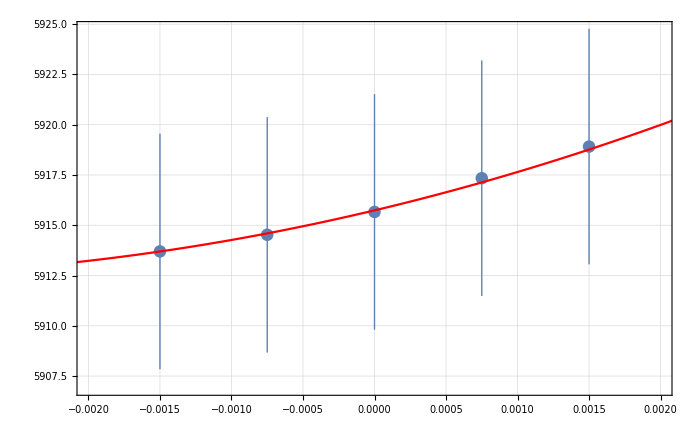
{{{5.9137×10^-6,5.91453×10^-6,5.91566×10^-6,5.91734×10^-6,5.91891×10^-6},{5.85804×10^-9,5.85752×10^-9,5.85732×10^-9,5.85805×10^-9,5.85832×10^-9}},b0 =  | -0.00388164
FittedModel[5.91246×10^-6+0.000217698 (0.00388164+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.00388164 | 0.0499497 | -0.0777111 | 0.945133
scale | 0.000217698 | 0.00278326 | 0.078217 | 0.944777
yoffset | 5.91246×10^-6 | 4.00573×10^-8 | 147.6 | 0.0000458984 | 
 | DF | SS | MS
Model | 3 | 5.09981×10^6 | 1.69994×10^6
Error | 2 | 0.00225524 | 0.00112762
Uncorrected Total | 5 | 5.09981×10^6 | 
Corrected Total | 4 | 0.520555 |  | ,-Graphics-}

```mathematica
AlphaInvest=TransferToRefParableFit[RefSpectrum[[All,2]],AlphaDataList,bList, 4]
```

```mathematica
AlphaInvest[[2,1,1,2]]/(0.25)
```

-0.0155266

### check difference in drift distance spectrum

```mathematica
InterOrder=1;
```

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}],InterpolationOrder->InterOrder];
```

```mathematica
dAlphaSpectrumb0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumb0[[All,2]]/Total[dAlphaSpectrumb0[[All,2]]]}],InterpolationOrder->InterOrder];dAlphaSpectrumb75Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumb75[[All,2]]/Total[dAlphaSpectrumb75[[All,2]]]}],InterpolationOrder->InterOrder];
dAlphaSpectrumbm75Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumbm75[[All,2]]/Total[dAlphaSpectrumbm75[[All,2]]]}],InterpolationOrder->InterOrder];
dAlphaSpectrumb15Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumb15[[All,2]]/Total[dAlphaSpectrumb15[[All,2]]]}],InterpolationOrder->InterOrder];
dAlphaSpectrumbm15Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumbm15[[All,2]]/Total[dAlphaSpectrumbm15[[All,2]]]}],InterpolationOrder->InterOrder];
```

```mathematica
Plot3D[RefSpectrumInter[x,y]-dAlphaSpectrumb15Inter[x,y],{x,-0.04,0.04},{y,-0.05,0.05},PlotRange->All]
```

-Graphics3D-

```mathematica
ytest=0.0;
```

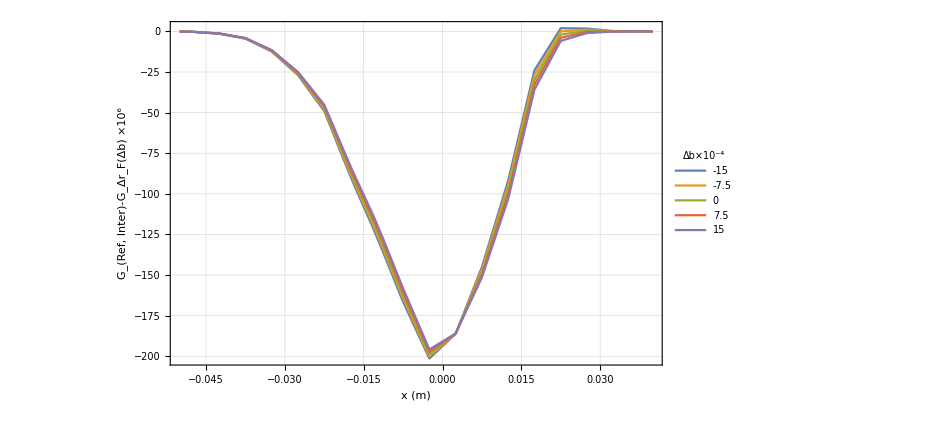

```mathematica
DeltaGxdbPlot=Plot[{
10^6*(RefSpectrumInter[x,ytest]-dAlphaSpectrumbm15Inter[x,ytest]),
10^6*(RefSpectrumInter[x,ytest]-dAlphaSpectrumbm75Inter[x,ytest]),
10^6*(RefSpectrumInter[x,ytest]-dAlphaSpectrumb0Inter[x,ytest]),
10^6*(RefSpectrumInter[x,ytest]-dAlphaSpectrumb75Inter[x,ytest]),
10^6*(RefSpectrumInter[x,ytest]-dAlphaSpectrumb15Inter[x,ytest])
}
,{x,-0.05,0.04},PlotRange->All,ImageSize->700,BaseStyle->25,FrameLabel->{{"G_(Ref, Inter)-G_Δr_F(Δb) ×10^6",None},{"x (m)","Difference in drift distance spectra by deviation Δr_F/r_F=1×10^-4"}},PlotLegends->Placed[LineLegend[{"-15","-7.5","0","7.5","15"},LegendLabel->"Δb×10^-4",LabelStyle->25,LegendFunction->(Framed[#1, FrameMargins -> 0,Background->Directive[Opacity[1],White]] & )],{0.1,0.65}]]
```

```mathematica
(*Export["~/Dropbox/PhD/PhDLatex/Figures/DeltaGxdb.png",DeltaGxdbPlot,ImageResolution->450];*)
```

# dYRxBShift, 0.00038

```mathematica
dParameter="YRxBShift";
```

### b=0

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_d"<>dParameter<>"/b0/"];
```

```mathematica
dAlphaSubFileNamesb0=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_D_BSOn_dYRxBShift_b0_1-98.txt,TransferResult_08-09-20_NC_opt_D_BSOn_dYRxBShift_b0_99-106.txt,TransferResult_08-09-20_NC_opt_D_BSOn_dYRxBShift_b0_107-122.txt,TransferResult_08-09-20_NC_opt_D_BSOn_dYRxBShift_b0_123-138.txt,TransferResult_08-09-20_NC_opt_D_BSOn_dYRxBShift_b0_139-154.txt,TransferResult_08-09-20_NC_opt_D_BSOn_dYRxBShift_b0_155-178.txt,TransferResult_08-09-20_NC_opt_D_BSOn_dYRxBShift_b0_179-253.txt}

```mathematica
dAlphaSpectrumb0=Flatten[Import[#,"Table"]&/@dAlphaSubFileNamesb0,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb0[[All,2]]}],PlotRange->All]*)
```

### b=15

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_d"<>dParameter<>"/b15/"];
```

```mathematica
dAlphaSubFileNamesb15=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_H_BSOn_dYRxBShift_b15_1-98.txt,TransferResult_08-09-20_NC_opt_H_BSOn_dYRxBShift_b15_99-106.txt,TransferResult_08-09-20_NC_opt_H_BSOn_dYRxBShift_b15_107-122.txt,TransferResult_08-09-20_NC_opt_H_BSOn_dYRxBShift_b15_123-138.txt,TransferResult_08-09-20_NC_opt_H_BSOn_dYRxBShift_b15_139-154.txt,TransferResult_08-09-20_NC_opt_H_BSOn_dYRxBShift_b15_155-178.txt,TransferResult_08-09-20_NC_opt_H_BSOn_dYRxBShift_b15_179-253.txt}

```mathematica
dAlphaSpectrumb15=Flatten[Import[#,"Table"]&/@dAlphaSubFileNamesb15,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumb0[[All,2]]}],PlotRange->All]*)
```

### b=7.5

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_d"<>dParameter<>"/b7/"];
```

```mathematica
dAlphaSubFileNamesb75=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_C_BSOn_dYRxBShift_b7_1-98.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dYRxBShift_b7_99-106.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dYRxBShift_b7_107-122.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dYRxBShift_b7_123-138.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dYRxBShift_b7_139-154.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dYRxBShift_b7_155-178.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dYRxBShift_b7_179-253.txt}

```mathematica
dAlphaSpectrumb75=Flatten[Import[#,"Table"]&/@dAlphaSubFileNamesb75,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumb75[[All,2]]}],PlotRange->All]*)
```

### b=-7.5

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_d"<>dParameter<>"/b-7/"];
```

```mathematica
dAlphaSubFileNamesbm75=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_C_BSOn_dYRxBShift_b-7_1-98.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dYRxBShift_b-7_99-106.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dYRxBShift_b-7_107-122.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dYRxBShift_b-7_123-138.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dYRxBShift_b-7_139-154.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dYRxBShift_b-7_155-178.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dYRxBShift_b-7_179-253.txt}

```mathematica
dAlphaSpectrumbm75=Flatten[Import[#,"Table"]&/@dAlphaSubFileNamesbm75,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumbm75[[All,2]]}],PlotRange->All]*)
```

### b=-15

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_d"<>dParameter<>"/b-15/"];
```

```mathematica
dAlphaSubFileNamesbm15=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_G_BSOn_dYRxBShift_b-15_1-98.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dYRxBShift_b-15_99-106.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dYRxBShift_b-15_107-122.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dYRxBShift_b-15_123-138.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dYRxBShift_b-15_139-154.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dYRxBShift_b-15_155-178.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dYRxBShift_b-15_179-253.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
dAlphaSpectrumbm15=Flatten[Import[#,"Table"]&/@dAlphaSubFileNamesbm15,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumbm15[[All,2]]}],PlotRange->All]
```

-Graphics3D-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFit]
```

```mathematica
Get["Common/CommonFunctions.m"]
```

```mathematica
AlphaDataList={dAlphaSpectrumbm15[[All,2]]/Total[dAlphaSpectrumbm15[[All,2]]],dAlphaSpectrumbm75[[All,2]]/Total[dAlphaSpectrumbm75[[All,2]]],dAlphaSpectrumb0[[All,2]]/Total[dAlphaSpectrumb0[[All,2]]],dAlphaSpectrumb75[[All,2]]/Total[dAlphaSpectrumb75[[All,2]]],dAlphaSpectrumb15[[All,2]]/Total[dAlphaSpectrumb15[[All,2]]]};
```

```mathematica
bList={-15,-7.5,0.,7.5,15}*10^-4.
```

{-0.0015,-0.00075,0.,0.00075,0.0015}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

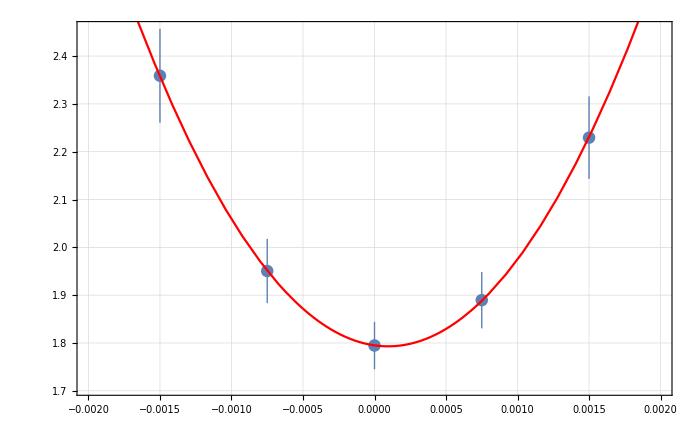
{{{2.35885×10^-9,1.95051×10^-9,1.79473×10^-9,1.88959×10^-9,2.22942×10^-9},{9.81914×10^-11,6.72212×10^-11,4.95175×10^-11,5.89583×10^-11,8.62225×10^-11}},b0 =  | 0.0000952392
FittedModel[1.79305×10^-9+0.000221819 (-0.0000952392+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | 0.0000952392 | 0.0000795102 | 1.19782 | 0.353686
scale | 0.000221819 | 0.0000358823 | 6.18186 | 0.0251832
yoffset | 1.79305×10^-9 | 3.87781×10^-11 | 46.2389 | 0.000467391 | 
 | DF | SS | MS
Model | 3 | 4428.44 | 1476.15
Error | 2 | 0.0013003 | 0.000650149
Uncorrected Total | 5 | 4428.44 | 
Corrected Total | 4 | 38.721 |  | ,-Graphics-}

```mathematica
AlphaInvest=TransferToRefParableFit[RefSpectrum[[All,2]],AlphaDataList,bList, 4]
```

```mathematica
AlphaInvest[[2,1,1,2]]/(0.25)
```

0.000380957

### check difference in drift distance spectrum

```mathematica
InterOrder=1;
```

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}],InterpolationOrder->InterOrder];
```

```mathematica
dAlphaSpectrumb0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumb0[[All,2]]/Total[dAlphaSpectrumb0[[All,2]]]}],InterpolationOrder->InterOrder];dAlphaSpectrumb75Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumb75[[All,2]]/Total[dAlphaSpectrumb75[[All,2]]]}],InterpolationOrder->InterOrder];
dAlphaSpectrumbm75Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumbm75[[All,2]]/Total[dAlphaSpectrumbm75[[All,2]]]}],InterpolationOrder->InterOrder];
dAlphaSpectrumb15Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumb15[[All,2]]/Total[dAlphaSpectrumb15[[All,2]]]}],InterpolationOrder->InterOrder];
dAlphaSpectrumbm15Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumbm15[[All,2]]/Total[dAlphaSpectrumbm15[[All,2]]]}],InterpolationOrder->InterOrder];
```

```mathematica
Plot3D[RefSpectrumInter[x,y]-dAlphaSpectrumb15Inter[x,y],{x,-0.04,0.04},{y,-0.05,0.05},PlotRange->All]
```

-Graphics3D-

```mathematica
ytest=0.0;
```

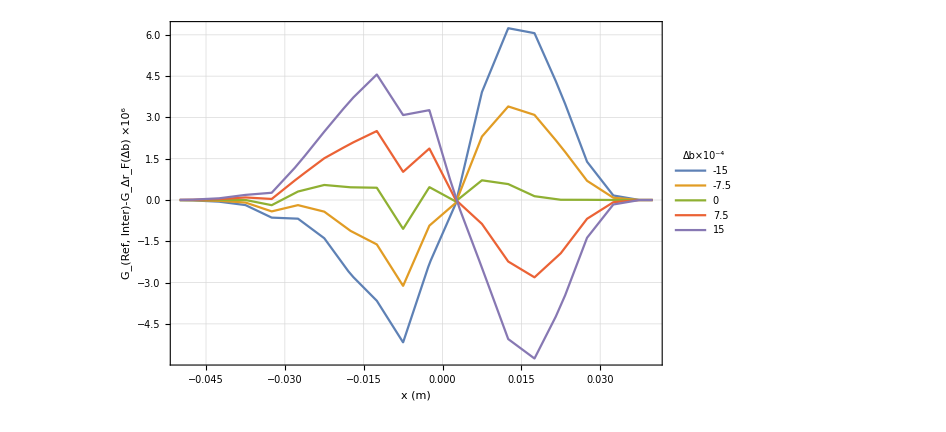

```mathematica
DeltaGxdbPlot=Plot[{
10^6*(RefSpectrumInter[x,ytest]-dAlphaSpectrumbm15Inter[x,ytest]),
10^6*(RefSpectrumInter[x,ytest]-dAlphaSpectrumbm75Inter[x,ytest]),
10^6*(RefSpectrumInter[x,ytest]-dAlphaSpectrumb0Inter[x,ytest]),
10^6*(RefSpectrumInter[x,ytest]-dAlphaSpectrumb75Inter[x,ytest]),
10^6*(RefSpectrumInter[x,ytest]-dAlphaSpectrumb15Inter[x,ytest])
}
,{x,-0.05,0.04},PlotRange->All,ImageSize->700,BaseStyle->25,FrameLabel->{{"G_(Ref, Inter)-G_Δr_F(Δb) ×10^6",None},{"x (m)","Difference in drift distance spectra by deviation Δr_F/r_F=1×10^-4"}},PlotLegends->Placed[LineLegend[{"-15","-7.5","0","7.5","15"},LegendLabel->"Δb×10^-4",LabelStyle->25,LegendFunction->(Framed[#1, FrameMargins -> 0,Background->Directive[Opacity[1],White]] & )],{0.1,0.65}]]
```

```mathematica
(*Export["~/Dropbox/PhD/PhDLatex/Figures/DeltaGxdb.png",DeltaGxdbPlot,ImageResolution->450];*)
```

# dNk2x, 0.975

```mathematica
dParameter="Nk2x";
```

### b=0

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_d"<>dParameter<>"/b0/"];
```

```mathematica
dAlphaSubFileNamesb0=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_D_BSOn_dNk2x_b0_1-98.txt,TransferResult_08-09-20_NC_opt_D_BSOn_dNk2x_b0_99-106.txt,TransferResult_08-09-20_NC_opt_D_BSOn_dNk2x_b0_107-122.txt,TransferResult_08-09-20_NC_opt_D_BSOn_dNk2x_b0_123-138.txt,TransferResult_08-09-20_NC_opt_D_BSOn_dNk2x_b0_139-154.txt,TransferResult_08-09-20_NC_opt_D_BSOn_dNk2x_b0_155-178.txt,TransferResult_08-09-20_NC_opt_D_BSOn_dNk2x_b0_179-253.txt}

```mathematica
dAlphaSpectrumb0=Flatten[Import[#,"Table"]&/@dAlphaSubFileNamesb0,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb0[[All,2]]}],PlotRange->All]*)
```

### b=15

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_d"<>dParameter<>"/b15/"];
```

```mathematica
dAlphaSubFileNamesb15=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_G_BSOn_dNk2x_b15_1-98.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dNk2x_b15_99-106.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dNk2x_b15_107-122.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dNk2x_b15_123-138.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dNk2x_b15_139-154.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dNk2x_b15_155-178.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dNk2x_b15_179-253.txt}

```mathematica
dAlphaSpectrumb15=Flatten[Import[#,"Table"]&/@dAlphaSubFileNamesb15,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumb0[[All,2]]}],PlotRange->All]*)
```

### b=7.5

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_d"<>dParameter<>"/b7/"];
```

```mathematica
dAlphaSubFileNamesb75=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_C_BSOn_dNk2x_b7_1-98.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dNk2x_b7_99-106.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dNk2x_b7_107-122.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dNk2x_b7_123-138.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dNk2x_b7_139-154.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dNk2x_b7_155-178.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dNk2x_b7_179-253.txt}

```mathematica
dAlphaSpectrumb75=Flatten[Import[#,"Table"]&/@dAlphaSubFileNamesb75,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumb75[[All,2]]}],PlotRange->All]*)
```

### b=-7.5

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_d"<>dParameter<>"/b-7/"];
```

```mathematica
dAlphaSubFileNamesbm75=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_C_BSOn_dNk2x_b-7_1-98.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dNk2x_b-7_99-106.txt,TransferResult_08-09-20_NC_opt_H_BSOn_dNk2x_b-7_107-122.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dNk2x_b-7_123-138.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dNk2x_b-7_139-154.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dNk2x_b-7_155-178.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dNk2x_b-7_179-253.txt}

```mathematica
dAlphaSpectrumbm75=Flatten[Import[#,"Table"]&/@dAlphaSubFileNamesbm75,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumbm75[[All,2]]}],PlotRange->All]*)
```

### b=-15

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_d"<>dParameter<>"/b-15/"];
```

```mathematica
dAlphaSubFileNamesbm15=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_H_BSOn_dNk2x_b-15_1-98.txt,TransferResult_08-09-20_NC_opt_H_BSOn_dNk2x_b-15_99-106.txt,TransferResult_08-09-20_NC_opt_H_BSOn_dNk2x_b-15_107-122.txt,TransferResult_08-09-20_NC_opt_H_BSOn_dNk2x_b-15_123-138.txt,TransferResult_08-09-20_NC_opt_H_BSOn_dNk2x_b-15_139-154.txt,TransferResult_08-09-20_NC_opt_H_BSOn_dNk2x_b-15_155-178.txt,TransferResult_08-09-20_NC_opt_H_BSOn_dNk2x_b-15_179-253.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
dAlphaSpectrumbm15=Flatten[Import[#,"Table"]&/@dAlphaSubFileNamesbm15,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumbm15[[All,2]]}],PlotRange->All]
```

-Graphics3D-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFit]
```

```mathematica
Get["Common/CommonFunctions.m"]
```

```mathematica
AlphaDataList={dAlphaSpectrumbm15[[All,2]]/Total[dAlphaSpectrumbm15[[All,2]]],dAlphaSpectrumbm75[[All,2]]/Total[dAlphaSpectrumbm75[[All,2]]],dAlphaSpectrumb0[[All,2]]/Total[dAlphaSpectrumb0[[All,2]]],dAlphaSpectrumb75[[All,2]]/Total[dAlphaSpectrumb75[[All,2]]],dAlphaSpectrumb15[[All,2]]/Total[dAlphaSpectrumb15[[All,2]]]};
```

```mathematica
bList={-15,-7.5,0.,7.5,15}*10^-4.
```

{-0.0015,-0.00075,0.,0.00075,0.0015}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

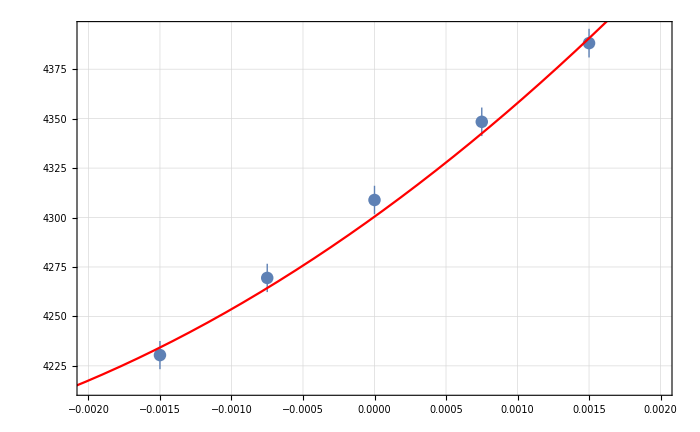
{{{4.23045×10^-6,4.26946×10^-6,4.30887×10^-6,4.3484×10^-6,4.38818×10^-6},{7.12753×10^-9,7.15821×10^-9,7.18919×10^-9,7.22006×10^-9,7.25065×10^-9}},b0 =  | -0.0048731
FittedModel[4.17343×10^-6+0.0053478 (0.0048731+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.0048731 | 0.00312255 | -1.56062 | 0.25899
scale | 0.0053478 | 0.00341572 | 1.56564 | 0.257918
yoffset | 4.17343×10^-6 | 7.85817×10^-8 | 53.1094 | 0.000354345 | 
 | DF | SS | MS
Model | 3 | 1.79626×10^6 | 598753.
Error | 2 | 2.95882 | 1.47941
Uncorrected Total | 5 | 1.79626×10^6 | 
Corrected Total | 4 | 300.98 |  | ,-Graphics-}

```mathematica
AlphaInvest=TransferToRefParableFit[RefSpectrum[[All,2]],AlphaDataList,bList, 4]
```

```mathematica
AlphaInvest[[2,1,1,2]]/(0.005)
```

-0.97462

```mathematica
%*0.001//ScientificForm
```

-9.7462×10^-4

### check difference in drift distance spectrum

```mathematica
InterOrder=1;
```

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}],InterpolationOrder->InterOrder];
```

```mathematica
dAlphaSpectrumb0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumb0[[All,2]]/Total[dAlphaSpectrumb0[[All,2]]]}],InterpolationOrder->InterOrder];dAlphaSpectrumb75Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumb75[[All,2]]/Total[dAlphaSpectrumb75[[All,2]]]}],InterpolationOrder->InterOrder];
dAlphaSpectrumbm75Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumbm75[[All,2]]/Total[dAlphaSpectrumbm75[[All,2]]]}],InterpolationOrder->InterOrder];
dAlphaSpectrumb15Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumb15[[All,2]]/Total[dAlphaSpectrumb15[[All,2]]]}],InterpolationOrder->InterOrder];
dAlphaSpectrumbm15Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumbm15[[All,2]]/Total[dAlphaSpectrumbm15[[All,2]]]}],InterpolationOrder->InterOrder];
```

```mathematica
Plot3D[RefSpectrumInter[x,y]-dAlphaSpectrumb15Inter[x,y],{x,-0.04,0.04},{y,-0.05,0.05},PlotRange->All]
```

-Graphics3D-

```mathematica
ytest=0.0;
```

```mathematica
DeltaGxdbPlot=Plot[{
10^6*(RefSpectrumInter[x,ytest]-dAlphaSpectrumbm15Inter[x,ytest]),
10^6*(RefSpectrumInter[x,ytest]-dAlphaSpectrumbm75Inter[x,ytest]),
10^6*(RefSpectrumInter[x,ytest]-dAlphaSpectrumb0Inter[x,ytest]),
10^6*(RefSpectrumInter[x,ytest]-dAlphaSpectrumb75Inter[x,ytest]),
10^6*(RefSpectrumInter[x,ytest]-dAlphaSpectrumb15Inter[x,ytest])
}
,{x,-0.05,0.04},PlotRange->All,ImageSize->700,BaseStyle->25,FrameLabel->{{"G_(Ref, Inter)-G_Δr_F(Δb) ×10^6",None},{"x (m)","Difference in drift distance spectra by deviation Δr_F/r_F=1×10^-4"}},PlotLegends->Placed[LineLegend[{"-15","-7.5","0","7.5","15"},LegendLabel->"Δb×10^-4",LabelStyle->25,LegendFunction->(Framed[#1, FrameMargins -> 0,Background->Directive[Opacity[1],White]] & )],{0.1,0.65}]]
```

-Graphics-

```mathematica
(*Export["~/Dropbox/PhD/PhDLatex/Figures/DeltaGxdb.png",DeltaGxdbPlot,ImageResolution->450];*)
```

# dxAOff, 22

```mathematica
dParameter="xAOff";
```

### b=0

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_d"<>dParameter<>"/b0/"];
```

```mathematica
dAlphaSubFileNamesb0=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_C_BSOn_dxAOff_b0_1-98.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dxAOff_b0_99-106.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dxAOff_b0_107-122.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dxAOff_b0_123-138.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dxAOff_b0_139-154.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dxAOff_b0_155-178.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dxAOff_b0_179-253.txt}

```mathematica
dAlphaSpectrumb0=Flatten[Import[#,"Table"]&/@dAlphaSubFileNamesb0,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb0[[All,2]]}],PlotRange->All]*)
```

### b=15

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_d"<>dParameter<>"/b15/"];
```

```mathematica
dAlphaSubFileNamesb15=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_G_BSOn_dxAOff_b15_1-98.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dxAOff_b15_99-106.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dxAOff_b15_107-122.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dxAOff_b15_123-138.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dxAOff_b15_139-154.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dxAOff_b15_155-178.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dxAOff_b15_179-253.txt}

```mathematica
dAlphaSpectrumb15=Flatten[Import[#,"Table"]&/@dAlphaSubFileNamesb15,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumb0[[All,2]]}],PlotRange->All]*)
```

### b=7.5

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_d"<>dParameter<>"/b7/"];
```

```mathematica
dAlphaSubFileNamesb75=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_C_BSOn_dxAOff_b7_1-98.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dxAOff_b7_99-106.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dxAOff_b7_107-122.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dxAOff_b7_123-138.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dxAOff_b7_139-154.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dxAOff_b7_155-178.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dxAOff_b7_179-253.txt}

```mathematica
dAlphaSpectrumb75=Flatten[Import[#,"Table"]&/@dAlphaSubFileNamesb75,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumb75[[All,2]]}],PlotRange->All]*)
```

### b=-7.5

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_d"<>dParameter<>"/b-7/"];
```

```mathematica
dAlphaSubFileNamesbm75=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_C_BSOn_dxAOff_b-7_1-98.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dxAOff_b-7_99-106.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dxAOff_b-7_107-122.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dxAOff_b-7_123-138.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dxAOff_b-7_139-154.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dxAOff_b-7_155-178.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dxAOff_b-7_179-253.txt}

```mathematica
dAlphaSpectrumbm75=Flatten[Import[#,"Table"]&/@dAlphaSubFileNamesbm75,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumbm75[[All,2]]}],PlotRange->All]*)
```

### b=-15

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_d"<>dParameter<>"/b-15/"];
```

```mathematica
dAlphaSubFileNamesbm15=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_G_BSOn_dxAOff_b-15_1-98.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dxAOff_b-15_99-106.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dxAOff_b-15_107-122.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dxAOff_b-15_123-138.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dxAOff_b-15_139-154.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dxAOff_b-15_155-178.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dxAOff_b-15_179-253.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
dAlphaSpectrumbm15=Flatten[Import[#,"Table"]&/@dAlphaSubFileNamesbm15,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumbm15[[All,2]]}],PlotRange->All]
```

-Graphics3D-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFit]
```

```mathematica
Get["Common/CommonFunctions.m"]
```

```mathematica
AlphaDataList={dAlphaSpectrumbm15[[All,2]]/Total[dAlphaSpectrumbm15[[All,2]]],dAlphaSpectrumbm75[[All,2]]/Total[dAlphaSpectrumbm75[[All,2]]],dAlphaSpectrumb0[[All,2]]/Total[dAlphaSpectrumb0[[All,2]]],dAlphaSpectrumb75[[All,2]]/Total[dAlphaSpectrumb75[[All,2]]],dAlphaSpectrumb15[[All,2]]/Total[dAlphaSpectrumb15[[All,2]]]};
```

```mathematica
bList={-15,-7.5,0.,7.5,15}*10^-4.
```

{-0.0015,-0.00075,0.,0.00075,0.0015}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

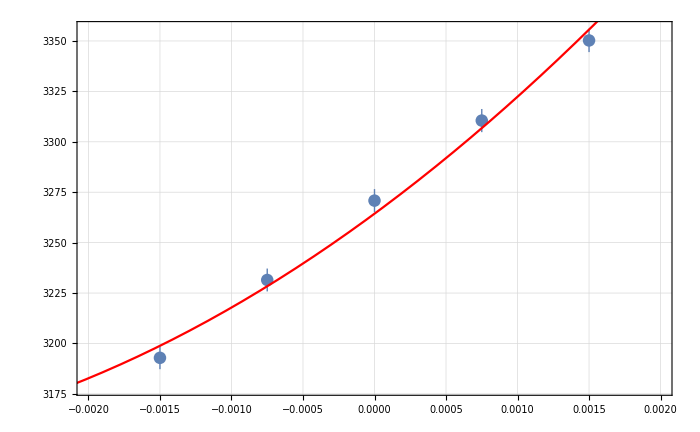
{{{3.19288×10^-6,3.23148×10^-6,3.27083×10^-6,3.31052×10^-6,3.35026×10^-6},{5.62807×10^-9,5.66636×10^-9,5.70481×10^-9,5.74289×10^-9,5.78115×10^-9}},b0 =  | -0.00455859
FittedModel[3.14521×10^-6+0.00573271 (0.00455859+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.00455859 | 0.00216212 | -2.10839 | 0.169521
scale | 0.00573271 | 0.00271036 | 2.11511 | 0.168702
yoffset | 3.14521×10^-6 | 5.42707×10^-8 | 57.9541 | 0.000297604 | 
 | DF | SS | MS
Model | 3 | 1.64394×10^6 | 547979.
Error | 2 | 4.01511 | 2.00755
Uncorrected Total | 5 | 1.64394×10^6 | 
Corrected Total | 4 | 476.517 |  | ,-Graphics-}

```mathematica
AlphaInvest=TransferToRefParableFit[RefSpectrum[[All,2]],AlphaDataList,bList, 4]
```

```mathematica
AlphaInvest[[2,1,1,2]]/(0.0004)
```

-11.3965

```mathematica
%*0.0002//ScientificForm
```

-2.2793×10^-3

### check difference in drift distance spectrum

```mathematica
InterOrder=1;
```

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}],InterpolationOrder->InterOrder];
```

```mathematica
dAlphaSpectrumb0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumb0[[All,2]]/Total[dAlphaSpectrumb0[[All,2]]]}],InterpolationOrder->InterOrder];dAlphaSpectrumb75Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumb75[[All,2]]/Total[dAlphaSpectrumb75[[All,2]]]}],InterpolationOrder->InterOrder];
dAlphaSpectrumbm75Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumbm75[[All,2]]/Total[dAlphaSpectrumbm75[[All,2]]]}],InterpolationOrder->InterOrder];
dAlphaSpectrumb15Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumb15[[All,2]]/Total[dAlphaSpectrumb15[[All,2]]]}],InterpolationOrder->InterOrder];
dAlphaSpectrumbm15Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumbm15[[All,2]]/Total[dAlphaSpectrumbm15[[All,2]]]}],InterpolationOrder->InterOrder];
```

```mathematica
Plot3D[RefSpectrumInter[x,y]-dAlphaSpectrumb15Inter[x,y],{x,-0.04,0.04},{y,-0.05,0.05},PlotRange->All]
```

-Graphics3D-

```mathematica
ytest=0.0;
```

```mathematica
DeltaGxdbPlot=Plot[{
10^6*(RefSpectrumInter[x,ytest]-dAlphaSpectrumbm15Inter[x,ytest]),
10^6*(RefSpectrumInter[x,ytest]-dAlphaSpectrumbm75Inter[x,ytest]),
10^6*(RefSpectrumInter[x,ytest]-dAlphaSpectrumb0Inter[x,ytest]),
10^6*(RefSpectrumInter[x,ytest]-dAlphaSpectrumb75Inter[x,ytest]),
10^6*(RefSpectrumInter[x,ytest]-dAlphaSpectrumb15Inter[x,ytest])
}
,{x,-0.05,0.04},PlotRange->All,ImageSize->700,BaseStyle->25,FrameLabel->{{"G_(Ref, Inter)-G_Δr_F(Δb) ×10^6",None},{"x (m)","Difference in drift distance spectra by deviation Δr_F/r_F=1×10^-4"}},PlotLegends->Placed[LineLegend[{"-15","-7.5","0","7.5","15"},LegendLabel->"Δb×10^-4",LabelStyle->25,LegendFunction->(Framed[#1, FrameMargins -> 0,Background->Directive[Opacity[1],White]] & )],{0.1,0.65}]]
```

-Graphics-

```mathematica
(*Export["~/Dropbox/PhD/PhDLatex/Figures/DeltaGxdb.png",DeltaGxdbPlot,ImageResolution->450];*)
```

# dxAShift,

```mathematica
dParameter="XAShift";
```

### b=0

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_d"<>dParameter<>"/b0/"];
```

```mathematica
dAlphaSubFileNamesb0=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_D_BSOn_dXAShift_b0_1-98.txt,TransferResult_08-09-20_NC_opt_D_BSOn_dXAShift_b0_99-106.txt,TransferResult_08-09-20_NC_opt_D_BSOn_dXAShift_b0_107-122.txt,TransferResult_08-09-20_NC_opt_D_BSOn_dXAShift_b0_123-138.txt,TransferResult_08-09-20_NC_opt_D_BSOn_dXAShift_b0_139-154.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dXAShift_b0_155-178.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dXAShift_b0_179-253.txt}

```mathematica
dAlphaSpectrumb0=Flatten[Import[#,"Table"]&/@dAlphaSubFileNamesb0,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dBRxBSpectrumb0[[All,2]]}],PlotRange->All]*)
```

### b=15

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_d"<>dParameter<>"/b15/"];
```

```mathematica
dAlphaSubFileNamesb15=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_G_BSOn_dXAShift_b15_1-98.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dXAShift_b15_99-106.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dXAShift_b15_107-122.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dXAShift_b15_123-138.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dXAShift_b15_139-154.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dXAShift_b15_155-178.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dXAShift_b15_179-253.txt}

```mathematica
dAlphaSpectrumb15=Flatten[Import[#,"Table"]&/@dAlphaSubFileNamesb15,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumb0[[All,2]]}],PlotRange->All]*)
```

### b=7.5

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_d"<>dParameter<>"/b7/"];
```

```mathematica
dAlphaSubFileNamesb75=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_C_BSOn_dXAShift_b7_1-98.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dXAShift_b7_99-106.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dXAShift_b7_107-122.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dXAShift_b7_123-138.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dXAShift_b7_139-154.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dXAShift_b7_155-178.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dXAShift_b7_179-253.txt}

```mathematica
dAlphaSpectrumb75=Flatten[Import[#,"Table"]&/@dAlphaSubFileNamesb75,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumb75[[All,2]]}],PlotRange->All]*)
```

### b=-7.5

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_d"<>dParameter<>"/b-7/"];
```

```mathematica
dAlphaSubFileNamesbm75=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_C_BSOn_dXAShift_b-7_1-98.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dXAShift_b-7_99-106.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dXAShift_b-7_107-122.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dXAShift_b-7_123-138.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dXAShift_b-7_139-154.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dXAShift_b-7_155-178.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dXAShift_b-7_179-253.txt}

```mathematica
dAlphaSpectrumbm75=Flatten[Import[#,"Table"]&/@dAlphaSubFileNamesbm75,1];
```

```mathematica
(*ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumbm75[[All,2]]}],PlotRange->All]*)
```

### b=-15

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/MergerTransport/NC_opt_d"<>dParameter<>"/b-15/"];
```

```mathematica
dAlphaSubFileNamesbm15=FileSorter[""]
```

{TransferResult_08-09-20_NC_opt_H_BSOn_dXAShift_b-15_1-98.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dXAShift_b-15_99-106.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dXAShift_b-15_107-122.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dXAShift_b-15_123-138.txt,TransferResult_08-09-20_NC_opt_G_BSOn_dXAShift_b-15_139-154.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dXAShift_b-15_155-178.txt,TransferResult_08-09-20_NC_opt_C_BSOn_dXAShift_b-15_179-253.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
dAlphaSpectrumbm15=Flatten[Import[#,"Table"]&/@dAlphaSubFileNamesbm15,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumbm15[[All,2]]}],PlotRange->All]
```

-Graphics3D-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFit]
```

```mathematica
Get["Common/CommonFunctions.m"]
```

```mathematica
AlphaDataList={dAlphaSpectrumbm15[[All,2]]/Total[dAlphaSpectrumbm15[[All,2]]],dAlphaSpectrumbm75[[All,2]]/Total[dAlphaSpectrumbm75[[All,2]]],dAlphaSpectrumb0[[All,2]]/Total[dAlphaSpectrumb0[[All,2]]],dAlphaSpectrumb75[[All,2]]/Total[dAlphaSpectrumb75[[All,2]]],dAlphaSpectrumb15[[All,2]]/Total[dAlphaSpectrumb15[[All,2]]]};
```

```mathematica
bList={-15,-7.5,0.,7.5,15}*10^-4.
```

{-0.0015,-0.00075,0.,0.00075,0.0015}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

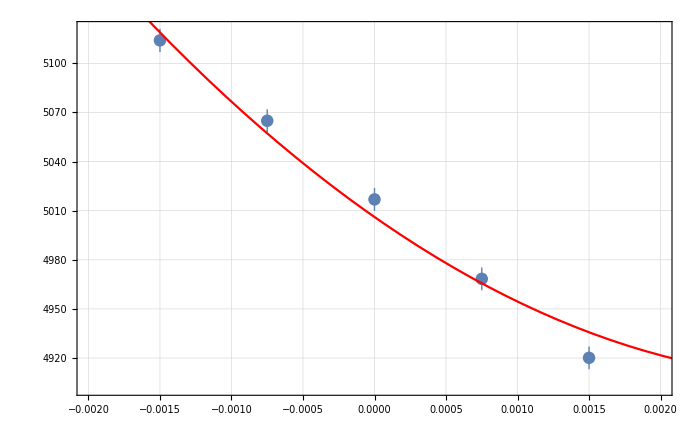
{{{5.11406×10^-6,5.06493×10^-6,5.0169×10^-6,4.96836×10^-6,4.92011×10^-6},{7.08701×10^-9,7.04863×10^-9,7.01165×10^-9,6.97334×10^-9,6.93508×10^-9}},b0 =  | 0.00324369
FittedModel[4.90709×10^-6+0.00941379 (-0.00324369+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | 0.00324369 | 0.0011565 | 2.80474 | 0.107086
scale | 0.00941379 | 0.00333116 | 2.82598 | 0.105728
yoffset | 4.90709×10^-6 | 3.27556×10^-8 | 149.809 | 0.0000445548 | 
 | DF | SS | MS
Model | 3 | 2.55996×10^6 | 853319.
Error | 2 | 9.23773 | 4.61887
Uncorrected Total | 5 | 2.55997×10^6 | 
Corrected Total | 4 | 477.527 |  | ,-Graphics-}

```mathematica
AlphaInvest=TransferToRefParableFit[RefSpectrum[[All,2]],AlphaDataList,bList, 4]
```

```mathematica
AlphaInvest[[2,1,1,2]]/(0.00025)
```

12.9747

```mathematica
%*0.0001//ScientificForm
```

1.29747×10^-3

### check difference in drift distance spectrum

```mathematica
InterOrder=1;
```

```mathematica
RefSpectrumInter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],RefSpectrum[[All,2]]/Total[RefSpectrum[[All,2]]]}],InterpolationOrder->InterOrder];
```

```mathematica
dAlphaSpectrumb0Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumb0[[All,2]]/Total[dAlphaSpectrumb0[[All,2]]]}],InterpolationOrder->InterOrder];dAlphaSpectrumb75Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumb75[[All,2]]/Total[dAlphaSpectrumb75[[All,2]]]}],InterpolationOrder->InterOrder];
dAlphaSpectrumbm75Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumbm75[[All,2]]/Total[dAlphaSpectrumbm75[[All,2]]]}],InterpolationOrder->InterOrder];
dAlphaSpectrumb15Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumb15[[All,2]]/Total[dAlphaSpectrumb15[[All,2]]]}],InterpolationOrder->InterOrder];
dAlphaSpectrumbm15Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],XYBinCentersYHalf[[All,2]],dAlphaSpectrumbm15[[All,2]]/Total[dAlphaSpectrumbm15[[All,2]]]}],InterpolationOrder->InterOrder];
```

```mathematica
Plot3D[RefSpectrumInter[x,y]-dAlphaSpectrumb15Inter[x,y],{x,-0.04,0.04},{y,-0.05,0.05},PlotRange->All]
```

-Graphics3D-

```mathematica
ytest=0.0;
```

```mathematica
DeltaGxdbPlot=Plot[{
10^6*(RefSpectrumInter[x,ytest]-dAlphaSpectrumbm15Inter[x,ytest]),
10^6*(RefSpectrumInter[x,ytest]-dAlphaSpectrumbm75Inter[x,ytest]),
10^6*(RefSpectrumInter[x,ytest]-dAlphaSpectrumb0Inter[x,ytest]),
10^6*(RefSpectrumInter[x,ytest]-dAlphaSpectrumb75Inter[x,ytest]),
10^6*(RefSpectrumInter[x,ytest]-dAlphaSpectrumb15Inter[x,ytest])
}
,{x,-0.05,0.04},PlotRange->All,ImageSize->700,BaseStyle->25,FrameLabel->{{"G_(Ref, Inter)-G_Δr_F(Δb) ×10^6",None},{"x (m)","Difference in drift distance spectra by deviation Δr_F/r_F=1×10^-4"}},PlotLegends->Placed[LineLegend[{"-15","-7.5","0","7.5","15"},LegendLabel->"Δb×10^-4",LabelStyle->25,LegendFunction->(Framed[#1, FrameMargins -> 0,Background->Directive[Opacity[1],White]] & )],{0.1,0.65}]]
```

-Graphics-

```mathematica
(*Export["~/Dropbox/PhD/PhDLatex/Figures/DeltaGxdb.png",DeltaGxdbPlot,ImageResolution->450];*)
```

# test

```mathematica
BackScatterBoole=True;
```

```mathematica
Get["MergerTransport/Merger2D.m"]
```

Set::wrsym: Symbol pmax is Protected.

```mathematica
?pminApertShift
```

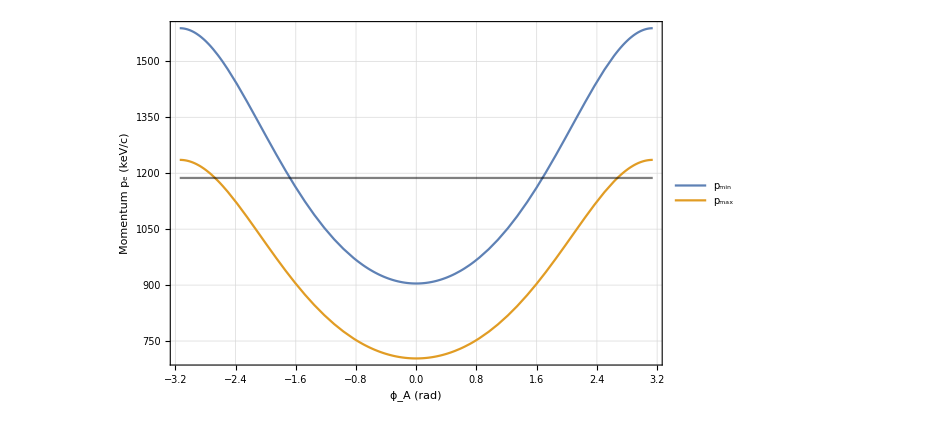

```mathematica
test=Show[
Plot[{1/1000*pminApertShift[phiA,0.,-0.01,Pi/4,Pi,0.22,1,1,1,0,1,1,0.03,0.01,{0.,0.006,0,0.015}],1/1000*pmaxApertShift[phiA,0.,-0.01,Pi/4,Pi,0.22,1,1,1,0,1,1,0.03,0.01,{0.,0.006,0,0.015}]},{phiA,-Pi,Pi},FrameLabel->{{"Momentum p_e (keV/c)",None},{"ϕ_A (rad)",None}},BaseStyle->25,ImageSize->700,PlotLegends->Placed[LineLegend[{"p_min","p_max"},LegendFunction->(Framed[#1, FrameMargins -> 0,Background->White] & )],{0.63,0.75}]],
Plot[pmax/1000,{p,-Pi,Pi},PlotStyle->Directive[Black,Opacity[0.5]]]
]
```

```mathematica
Export["~/Dropbox/PhD/PhDLatex/Figures/pminpmax.png",test,ImageResolution->450];
```

### try p limits from Y

```mathematica
pminApertY[phiA_,yD_,th0_,BRxB_,rRxB_,rA_,rD_,phiDet_,yOff_,yAA_,YAShift_,YDetShift_]=Module[{plocal},Solve[yOff+yAA/2==yAShift[phiA,yD,plocal,alpha,th0,BRxB,rRxB,rA,rD,phiDet,YAShift,YDetShift],plocal,Reals][[1,1,2,1]]]
```

(-149896229 BRxB rA yAA+299792458 BRxB rA YAShift+(299792458 BRxB √rD yD)/(√(1/rA))-(299792458 BRxB √rD YDetShift)/(√(1/rA))-299792458 BRxB rA yOff)/(-rRxB Sin[phiA] Sin[th0]+(rRxB Sin[phiDet] Sin[th0])/(√(1/rA) √rD))

```mathematica
pmaxApertY[phiA_,yD_,th0_,BRxB_,rRxB_,rA_,rD_,phiDet_,yOff_,yAA_,YAShift_,YDetShift_]=Module[{plocal},Solve[yOff-yAA/2==yAShift[phiA,yD,plocal,alpha,th0,BRxB,rRxB,rA,rD,phiDet,YAShift,YDetShift],plocal,Reals][[1,1,2,1]]]
```

(149896229 BRxB rA yAA+299792458 BRxB rA YAShift+(299792458 BRxB √rD yD)/(√(1/rA))-(299792458 BRxB √rD YDetShift)/(√(1/rA))-299792458 BRxB rA yOff)/(-rRxB Sin[phiA] Sin[th0]+(rRxB Sin[phiDet] Sin[th0])/(√(1/rA) √rD))

```mathematica
yDList=Table[yD,{yD,-0.04,0.04,0.0025}]
```

{-0.04,-0.0375,-0.035,-0.0325,-0.03,-0.0275,-0.025,-0.0225,-0.02,-0.0175,-0.015,-0.0125,-0.01,-0.0075,-0.005,-0.0025,0.,0.0025,0.005,0.0075,0.01,0.0125,0.015,0.0175,0.02,0.0225,0.025,0.0275,0.03,0.0325,0.035,0.0375,0.04}

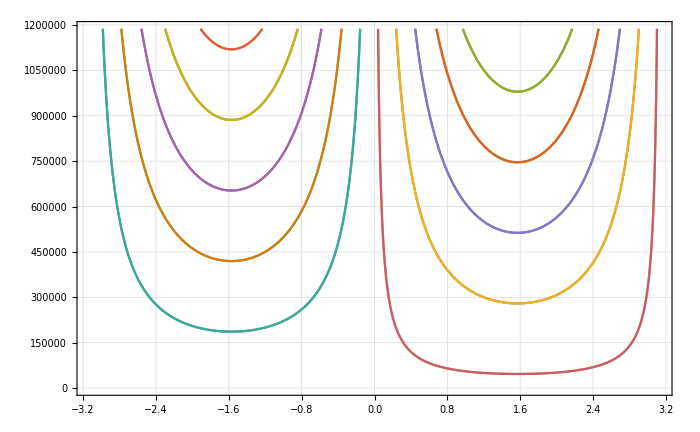

```mathematica
Show[Table[Plot[{pminApertY[phiA,yDList[[i]],Pi/4,0.22,1,1,1,0,0,0.035,0.007,0.015],pmaxApertY[phiA,yDList[[i]],Pi/4,0.22,1,1,1,0,0,0.035,0.007,0.015]},{phiA,-Pi,Pi},PlotRange->{0,pmax},PlotStyle->ColorData[97][i]],{i,33}]]
```

```mathematica
pYlimitfuncmin[yD_,th0_,BRxB_,rRxB_,rA_,rD_,phiDet_,yOff_,yAA_,YAShift_,YDetShift_]:=Cases[{pminApertY[-Pi/2,yD,th0,BRxB,rRxB,rA,rD,phiDet,yOff,yAA,YAShift,YDetShift],pminApertY[Pi/2,yD,th0,BRxB,rRxB,rA,rD,phiDet,yOff,yAA,YAShift,YDetShift]},_?(0<#<pmax&)]
```

```mathematica
pYlimitfuncmax[yD_,th0_,BRxB_,rRxB_,rA_,rD_,phiDet_,yOff_,yAA_,YAShift_,YDetShift_]:=Cases[{pmaxApertY[-Pi/2,yD,th0,BRxB,rRxB,rA,rD,phiDet,yOff,yAA,YAShift,YDetShift],pmaxApertY[Pi/2,yD,th0,BRxB,rRxB,rA,rD,phiDet,yOff,yAA,YAShift,YDetShift]},_?(0<#<pmax&)]
```

```mathematica
pYlimitfunc[yD_,th0_,BRxB_,rRxB_,rA_,rD_,phiDet_,yOff_,yAA_,YAShift_,YDetShift_]:=Join[pYlimitfuncmax[yD,th0,BRxB,rRxB,rA,rD,phiDet,yOff,yAA,YAShift,YDetShift],pYlimitfuncmax[yD,th0,BRxB,rRxB,rA,rD,phiDet,yOff,yAA,YAShift,YDetShift]]
```

```mathematica
pAllDomainShift[yD_?NumericQ,xD_?NumericQ,th0_?NumericQ,alpha_,BRxB_,rRxB_,rA_,rD_,phiDet_?NumericQ,G1_,G2_,{xAA_,yAA_,xOff_,yOff_},{XAShift_,YAShift_,YRxBShift_,XDetShift_,YDetShift_}]:={p,Sequence@@Union[pLimitsApertXListShift[yD,xD,th0,alpha,BRxB,rRxB,rA,rD,phiDet,G1,G2,xOff,xAA,{XAShift,YRxBShift,XDetShift,YDetShift}],pYlimitfunc[yD,th0,BRxB,rRxB,rA,rD,phiDet,yOff,yAA,YAShift,YDetShift]]}
```

```mathematica
pAllDomainShift[yDtest,xDtest,Pi/4,Pi,0.22,1,1,1,0,1,1,{0.01,0.035,0.03,0.},{0,0.007,0.006,0.,0.015}]
```

{p,503080.,704312.,755516.,884906.,1.18728×10^6}

### check p integrand with those limits

```mathematica
xDtest=0.;
```

```mathematica
yDtest=0.;
```

```mathematica
pYlimitfunc[yDtest]
```

{}

```mathematica
pYlimitfuncmax[yDtest]
```

{755516.}

```mathematica
pXlimits=pLimitsApertXListShift[yDtest,xDtest,Pi/4,Pi,0.22,1,1,1,0,1,1,0.03,0.01,{0,0.006,0.,0.015}]
```

{502365.,703311.,882697.,1.18728×10^6}

```mathematica
pLimitsApertXListShift[yDtest,xDtest,Pi/4,Pi,0.32,1,1,1,0,1,1,0.03,0.01,{0,0.006,0.,0.015}]
```

{730713.,1.023×10^6,1.18728×10^6}

```mathematica
{730713.0435427524,1.0229982609598533*^6,1.1872848094398074*^6}
```

{730713.,1.023×10^6,1.18728×10^6}

```mathematica
pYlimits=Join[pYlimitfunc[yDtest],pYlimitfuncmax[yDtest]]
```

{755516.}

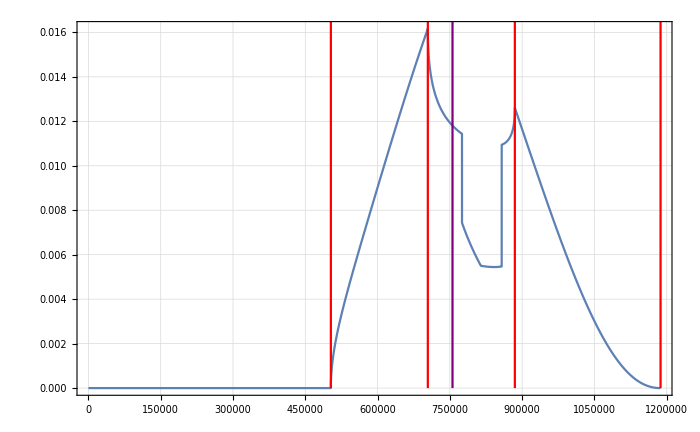

```mathematica
Show[
Plot[ManualphiAIntegrandAllLimitsShift[0.,yDtest,xDtest,{0.,0.,p,Pi/4},{Pi,0.22,1,1,1,1,1},{0,0.007,0.006,0,0.015},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.}],{p,0,pmax},PlotPoints->400],
ParametricPlot[{{#,p}&/@pXlimits},{p,0,pmax},PlotStyle->Red],
ParametricPlot[{{#,p}&/@Join[pYlimitfunc[yDtest],pYlimitfuncmax[yDtest]]},{p,0,pmax},PlotStyle->Purple]
]
```

```mathematica
RepeatedTiming[NIntegrate[
ManualphiAIntegrandAllLimitsShift[0.,yDtest,xDtest,{0.,0.,p,Pi/4},{Pi,0.22,1,1,1,1,1},{0,0.007,0.006,0,0.015},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.}],
{p,pXlimits[[1]],pXlimits[[2]],pXlimits[[3]],pXlimits[[4]]},PrecisionGoal->5,AccuracyGoal->2,MinRecursion->0,MaxRecursion->2]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in p near {p} = {884546.}. NIntegrate obtained 4892.4 and 31.7986 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.18,4892.4}

```mathematica
RepeatedTiming[NIntegrate[
ManualphiAIntegrandAllLimitsShift[0.,yDtest,xDtest,{0.,0.,p,Pi/4},{Pi,0.22,1,1,1,1,1},{0,0.007,0.006,0,0.015},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.}],
Evaluate[pXDomainShift[yDtest,xDtest,Pi/4,Pi,0.22,1,1,1,0,1,1,0.03,0.01,{0,0.006,0.,0.015}]],PrecisionGoal->5,AccuracyGoal->2,MinRecursion->0,MaxRecursion->2]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in p near {p} = {884546.}. NIntegrate obtained 4892.4 and 31.7986 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.19,4892.4}

```mathematica
IntegrationRules={"GaussBerntsenEspelidRule","GaussKronrodRule","LobattoKronrodRule","ClenshawCurtisRule"(*,"CartesianRule","MultidimensionalRule"*)};
IntegrationStrategies={"GlobalAdaptive","LocalAdaptive"};
IntOptionList=Flatten[Table[
{strategy,Method->rule},
{strategy,IntegrationStrategies},{rule,IntegrationRules}],1]
```

{{GlobalAdaptive,Method→GaussBerntsenEspelidRule},{GlobalAdaptive,Method→GaussKronrodRule},{GlobalAdaptive,Method→LobattoKronrodRule},{GlobalAdaptive,Method→ClenshawCurtisRule},{LocalAdaptive,Method→GaussBerntsenEspelidRule},{LocalAdaptive,Method→GaussKronrodRule},{LocalAdaptive,Method→LobattoKronrodRule},{LocalAdaptive,Method→ClenshawCurtisRule}}

```mathematica
woY=RepeatedTiming[NIntegrate[
ManualphiAIntegrandAllLimitsShift[0.,yDtest,xDtest,{0.,0.,p,Pi/4},{Pi,0.22,1,1,1,1,1},{0,0.007,0.006,0,0.015},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.}],
Evaluate[pXDomainShift[yDtest,xDtest,Pi/4,Pi,0.22,1,1,1,0,1,1,0.03,0.01,{0,0.006,0.,0.015}]],PrecisionGoal->4,AccuracyGoal->2,MinRecursion->0,MaxRecursion->8,Method->#]]&/@IntOptionList
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 8 recursive bisections in p near {p} = {858091.}. NIntegrate obtained 4900.94 and 1.5676 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 8 recursive bisections in p near {p} = {858091.}. NIntegrate obtained 4900.94 and 1.5676 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 8 recursive bisections in p near {p} = {858091.}. NIntegrate obtained 4900.94 and 1.5676 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{0.613,4900.94},{0.63,4900.96},{0.616,4901.25},{0.477,4901.27},{1.004,4801.17},{0.698,4900.96},{0.638,4900.84},{0.7315,4900.91}}

```mathematica
4901.247533579926*10^-4
```

0.490125

```mathematica
wY=RepeatedTiming[NIntegrate[
ManualphiAIntegrandAllLimitsShift[0.,yDtest,xDtest,{0.,0.,p,Pi/4},{Pi,0.22,1,1,1,1,1},{0,0.007,0.006,0,0.015},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.}],
Evaluate[pAllDomainShift[yDtest,xDtest,Pi/4,Pi,0.22,1,1,1,0,1,1,{0.01,0.035,0.03,0.},{0,0.007,0.006,0.,0.015}]],PrecisionGoal->4,AccuracyGoal->2,MinRecursion->0,MaxRecursion->8,Method->#]]&/@IntOptionList
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 8 recursive bisections in p near {p} = {857593.}. NIntegrate obtained 4900.94 and 0.548935 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{0.645,4900.88},{0.651,4900.85},{0.708,4900.72},{0.506,4900.94},{1.16,4809.24},{0.667,4900.84},{0.7365,4900.8},{0.9087,4900.82}}

```mathematica
woAll=RepeatedTiming[NIntegrate[
ManualphiAIntegrandAllLimitsShift[0.,yDtest,xDtest,{0.,0.,p,Pi/4},{Pi,0.22,1,1,1,1,1},{0,0.007,0.006,0,0.015},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{0.01,0.035,0.03,0.}],
{p,0,pmax},PrecisionGoal->4,AccuracyGoal->2,MinRecursion->0,MaxRecursion->8,Method->#]]&/@IntOptionList
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 8 recursive bisections in p near {p} = {779105.}. NIntegrate obtained 4901.26 and 4.76255 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 8 recursive bisections in p near {p} = {779105.}. NIntegrate obtained 4901.26 and 4.76255 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 8 recursive bisections in p near {p} = {779105.}. NIntegrate obtained 4901.26 and 4.76255 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{0.6,4901.26},{0.589,4900.6},{0.481,4900.2},{0.4,4902.28},{1.29,4798.61},{0.7374,4900.84},{0.88,4900.74},{1.173,4900.88}}

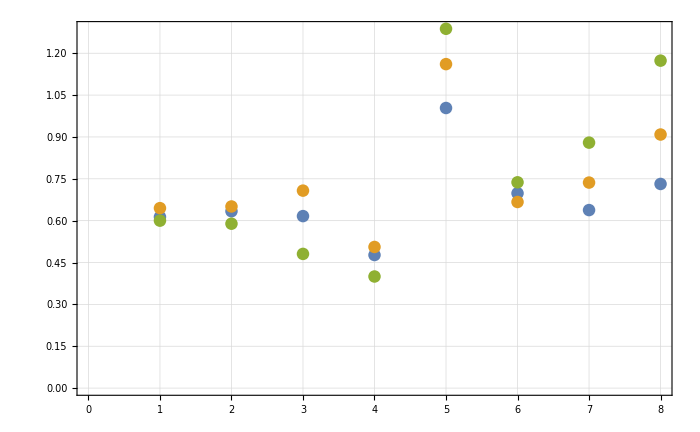

```mathematica
ListPlot[{woY[[All,1]],wY[[All,1]],woAll[[All,1]]}]
```

```mathematica
woY[[4,1]]/wY[[4,1]]
```

0.94

```mathematica
woAll[[4,2]]
```

4902.28

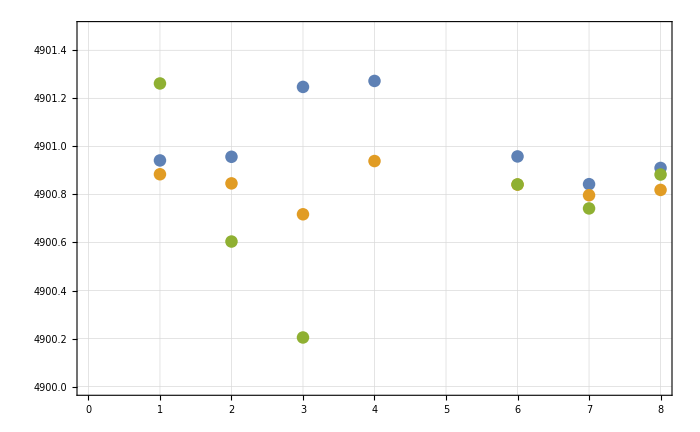

```mathematica
ListPlot[{woY[[All,2]],wY[[All,2]],woAll[[All,2]]}]
```